## A. GetVariance[ns, nph, Δprior] function

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
(*Δ here is centered around ϕ*)
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)
(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*The original integral (Check:1.3(Changes).nb): listOfϕ1 = Subscript[ϕ̃, m] = ParallelTable[ Integrate[ϕ listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Integrate[listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];*)
(*The denominator of this integral is Pm/Pϕ*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
Pm = Pϕ Table[Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 =
ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
(*finalVariance is the weighted average variance of all the probable outcomes*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*for feedfoward, we need to output the variance for each of the probable outcomes - no sum*)
(*different normalization term eq17*)
listOfPartialVarianceFeedforward =normalizationTerm*Table[Re[dummyFinalVariance1[[j]]], {j,1,(nph+1)^ns}];
(*conditional probabilities*)
(*Print[listOfPmϕ];*)
(*phase estimator after measurement assuming outcome m*)
listOfϕ1Feedforward = Table[r[[1,n]]^2*listOfϕ1[[n]],{n,1,nph+1}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
(*Return[finalVariance]*)
Return[listOfPartialVarianceFeedforward]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## B. Optimal input states functions

```mathematica
PlugN00NSBS[]:=
Block[{},
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
(*finalVarianceN00N=finalVariance/.substlistN00N;*)
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
(*Print[substlistN00N];*)
(*returns the variance and state to be plugged in*)
Return[{substlistN00N}];]
```

```mathematica
PlugGSBS[]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
(*finalVarianceG1=finalVariance/.substlistG1;*)
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[{substlistG1}];];
```

## (For check only) Adaptive global method - GetVffExact[NumShots_,NPhotons_,Δprior_]

```mathematica
GetVffExact[NumShots_,NPhotons_,Δprior_]:= 
Block[{IndVariance,rSubsList,θSubsList,listOfPmϕ,VffExact},
ns = NumShots;
nph = NPhotons;
Δ = Δprior;

IndVariance=GetVariance[ns,nph,Δ];
(*change variables of prob in such a way so as to differentiate between the two 1st shot outcomes*)
(*rVarChanged and θVarChanged need to be global since they are used in 3.ExtractOptState function*)
rVarChanged=Table[Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
θVarChanged=Table[Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
rSubsList = Transpose[Table[Table[r[[2,b]]-> rVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
θSubsList = Transpose[Table[Table[θ[[2,b]]-> θVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
(*Substitution list*)
SubsList = Table[Flatten[{rSubsList[[m1]],θSubsList[[m1]]}],{m1,1,nph+1}];
(*Substituting variables in the individual variance expressions*)
IndVarianceSub = Table[IndVariance[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
(*listOfPm2m1ϕ = P(m1|ϕ)P(m2|ϕ,m1)*)
listOfPmϕ;
(*listOfPm2m1ϕ = Table[listOfPmϕ[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];*)
(*Normalize probability*)
(*each product normalizes 1 probability term in the product (of listOfPm2m1ϕ); e.g (1 /(r0s1^2+r1s1^2)) normalizes Pm#ϕs1*)
ListOfnormalizationTerms = Table[1/(∑_(s=1)^(nph+1) (r[[1,s]])^2)1/(∑_(s=1)^(nph+1) (rVarChanged[[1,i,s]])^2),{i,1,nph+1}];
(*listOfPm2m1ϕ= Table[listOfPm2m1ϕ[[n]]*ListOfnormalizationTerms[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
Pm2m1 = Table[Integrate[Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];
ϕm2m1 = Table[Integrate[ϕ Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Pm2m1[[n]],{n,1,(nph+1)^ns}];*)
Wm = Table[ListOfnormalizationTerms[[Ceiling[m2/(nph+1)]]]*IndVarianceSub[[m2]],{m2,1,(nph+1)^ns}];
VffExactInd=Partition[Wm,nph+1];
VffExactIndSum = Table[Total[VffExactInd[[n]]],{n,1,nph+1}];
VffExact = Sum[Wm[[m1]],{m1,1,Length[Wm]}];
Return[VffExactIndSum]
]
```

#### Checks

```mathematica
(*Probability*)
```

```mathematica
Checksub=Flatten[{{θ0s1->2.851490288263774},{θ1s1->0.25304094804538657},{θ2s1->-1.4739933234649785},{θ0s2m1->-3.093399176686934},{θ1s2m1->1.553767334364549},{θ2s2m1->2.4567718694141494},{θ0s2m2->-3.0911976444251295},{θ1s2m2->1.670070365372295},{θ2s2m2->2.4969781506465303},{θ0s2m3->-2.0057741338419515},{θ1s2m3->1.9589500610781467},{θ2s2m3->-2.17469519303548},{r0s1->0.062327025905407174},{r1s1->0.7408594969868596},{r2s1->0.5277260482635109},{r0s2m1->0.2979036019318746},{r1s2m1->0.13897817556102043},{r2s2m1->0.2456424044272012},{r0s2m2->0.578500557504519},{r1s2m2->0.8314464160878037},{r2s2m2->0.10511807207960588},{r0s2m3->0.3259088817360256},{r1s2m3->0.2749830952433989},{r2s2m3->0.014299502030310274}}]
```

{θ0s1→2.85149,θ1s1→0.253041,θ2s1→-1.47399,θ0s2m1→-3.0934,θ1s2m1→1.55377,θ2s2m1→2.45677,θ0s2m2→-3.0912,θ1s2m2→1.67007,θ2s2m2→2.49698,θ0s2m3→-2.00577,θ1s2m3→1.95895,θ2s2m3→-2.1747,r0s1→0.062327,r1s1→0.740859,r2s1→0.527726,r0s2m1→0.297904,r1s2m1→0.138978,r2s2m1→0.245642,r0s2m2→0.578501,r1s2m2→0.831446,r2s2m2→0.105118,r0s2m3→0.325909,r1s2m3→0.274983,r2s2m3→0.0142995}

```mathematica
Sum[Pm2m1[[n]],{n,1,Length[Pm2m1]}]/.Checksub/.{Δ->π}
```

1.-2.11249×10^-18 ⅈ

```mathematica
(*Variance*)
```

## Simulation for MCA

### Comparing MC A with Analytic A, for N=4 (Scalable)

#### MC Adaptive

```mathematica
MCAVaryΔ = Table[VarRatioϕtrueGrid=Table[
ntrial=100;
listOfVarRatio=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =n π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Probability1stshot=prob2[[1,outcomeOccured]];
(*normalize variance*)
normalizedvariance=variance;
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{normalizedvariance/(initInterval^2/12),ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}
,{shot,1, nshots}],{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{initInterval, Mean[listOfVarRatio[[All,2,1]]],phitrue},{phitrue,-initInterval/3,initInterval/3,initInterval/10}];
(*mean VarRatio averaged over uniform grid of ϕtrue*)
Flatten[{initInterval, Mean[VarRatioϕtrueGrid[[All,2]]]}],{n,1,10}];
```

```mathematica
(*{ϕtrue, probability of 1shot outcome, probability of 2nd shot outcome, partial variance for the particular 1st shot outcome, 1st shot outcome*)
```

```mathematica
MCAVaryΔ
```

{{(3 π)/10,0.239592}}

```mathematica
(*unshifted*)
```

```mathematica
MCAVaryΔ
```

{{π/10,0.780884},{π/5,0.424319},{(3 π)/10,0.252959},{(2 π)/5,0.379188},{π/2,0.403363},{(3 π)/5,0.346102},{(7 π)/10,0.269283},{(4 π)/5,0.120117},{(9 π)/10,0.104458},{π,0.106912}}

```mathematica
(*partially shifted*)
```

{0.77419,0.443015,0.236116,0.349789,0.353799,0.27781,0.292475,0.110457,0.1135,0.0786249}

```mathematica
(*shifted then shifted back*)
```

```mathematica
MCAVaryΔ
```

{{π/10,0.773328},{π/5,0.491624},{(3 π)/10,0.358557},{(2 π)/5,0.329291},{π/2,0.305011},{(3 π)/5,0.27046},{(7 π)/10,0.220728},{(4 π)/5,0.139238},{(9 π)/10,0.121355},{π,0.113099}}

```mathematica
MCAVaryΔ
```

{{π/10,0.772973},{π/5,0.495898},{(3 π)/10,0.358557},{(2 π)/5,0.332479},{π/2,0.297404},{(3 π)/5,0.273461},{(7 π)/10,0.212571},{(4 π)/5,0.140663},{(9 π)/10,0.120222},{π,0.113232}}

#### VarRatio MCSA, MCA with sbs optimal states plugged into global variance N=4, ns=2

```mathematica
(*Non-adaptive global*)
```

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
(*MonteCarlo Semi-Adaptive*)
```

```mathematica
MCSAPlugged={0.7832548199807943,0.44909545514972116,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.28673863672037136,0.23189593990295332,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*Semi-adaptive*)
```

```mathematica
AnalyticSA={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*MonteCarlo Adaptive 100 trials of 10 phitrue intervals (1000 total)*)
```

```mathematica
MCAPluggedScalable100unshifted=MCAVaryΔ[[All,2]]
```

{0.780884,0.424319,0.252959,0.379188,0.403363,0.346102,0.269283,0.120117,0.104458,0.106912}

```mathematica
MCAPluggedScalable100shifted=MCAVaryΔ[[All,2]]
```

{0.772973,0.495898,0.358557,0.332479,0.297404,0.273461,0.212571,0.140663,0.120222,0.113232}

```mathematica
(*Adaptive*)
```

```mathematica
AnalyticA ={0.7848048836429581,0.4669568863147173,0.29662564242447337,0.29568912007540094,0.2519147001923571,0.19472241150788455,0.16801400651733248,0.12769682385452574,0.11170264823418144,0.1024495735826159}
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

```mathematica
(*State is shifted then shifted back*)
```

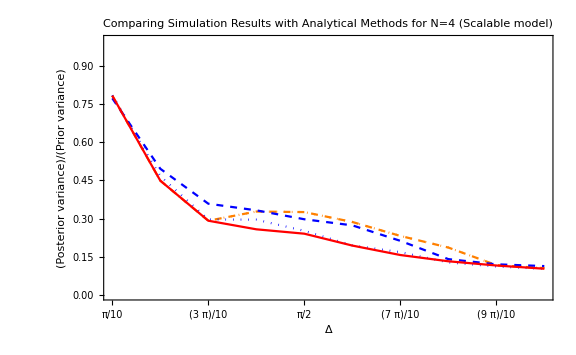

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPluggedScalable100shifted,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 100 trials of 10 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Scalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

```mathematica
(*Unshifted state used*)
```

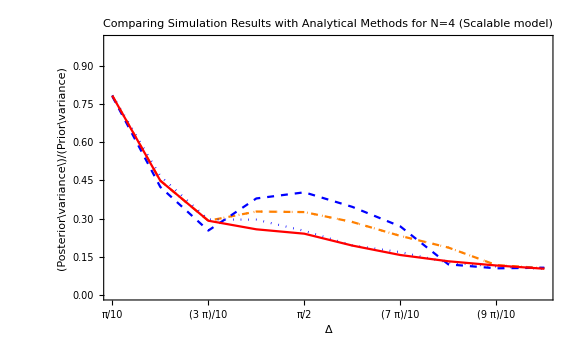

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPluggedScalable100unshifted,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 100 trials of 10 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior\variance\)/(Prior\variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Scalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

### Comparing MC A with Analytic A, for N=4 (unscalable - plug apt states into global variance)

#### MC Adaptive

```mathematica
MCAVaryΔ=Table[
ntrial=10;
MCATrial=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =n π/10;
GlobalVarianceA=GetVffExact[2,nph,initInterval];
VarRatio=Table[
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{variance,phitrue,ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}
,{shot,1, nshots}];
(*save the 2 shot outcomes*)
TwoShotOutcomesFixed={phitilde[[1,6]],phitilde[[2,6]]};
(*1st shot outcome*)
OutcomeOccured1stShot=phitilde[[1,6]];
(*For the first shot*)
Shot1AptStateList=phitilde[[1,5,1]];
Shot2AptStatetempList=phitilde[[2,5,1]];
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*Change variable names for second shot*)
Shot2AptStateList=Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[n,2]],r[[2,n]]-> Shot2AptStatetempList[[n+nph+1,2]]},{n,1,nph+1}]];
(*Substitution list*)
AptStates = Join[Shot1AptStateList,Shot2AptStateList];
(*Calculate the average phase estimator after 100 trials of 2 shots*)
ϕm1m2=phitilde[[2,3]];
(*outcome, probability1, probability2*)
probability1= {phitilde[[1,8]],phitilde[[2,8]]};
(*1st shot probability*)
Probability1stshot=phitilde[[1,8]][[1,OutcomeOccured1stShot]];
(*Normalized variance*)
variance2=GlobalVarianceA[[OutcomeOccured1stShot]]/.AptStates;
normalizedvariance=variance2/Probability1stshot;
(*VarianceRatio*)
BMSERatio = normalizedvariance/(initInterval^2/12);
(*ϕTrue, probability of 1st shot outcomes, probability of 2nd shot outcomes, variance*)
{phitrue,probability1,variance2,OutcomeOccured1stShot,BMSERatio},{phitrue,-initInterval/2,initInterval/2,initInterval/100}];
PartialVariances=VarRatio[[All,3]];
normalizedPartialVariance=Mean[VarRatio[[All,5]]];
normalizedPartialVariance,{trial,1,ntrial}];
Mean[MCATrial],{n,1,10}];
```

$Aborted

```mathematica
GlobalVarianceA[[OutcomeOccured1stShot]]
```

(10 Re[5+2 (-(3 ⅇ^(ⅈ θ0s1+5) (12/5 (-1-√5) π-√1 1) r0s1 r0s2m4 r4s1 r4s2m4)/32768+1/10368+5+1/48 (1) (6/5 π Cos[(3 π)/20]+(-8+(9 1)/100) Sin[1/20]))])/(3 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)+(10 Re[1])/(3 π (r0s1^2+3+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)+(10 Re[1])/(3 π 1^2 (1)^2)+(10 Re[5+2 (1)])/(3 π (1)^2 (r0s2m4^2+3+r4s2m4^2)^2)+(10 Re[5+2 (-(ⅇ^1 4 r4s2m4)/65536+6+1/288 (1) (1))])/(3 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)
 |  |  |  |

```mathematica
(*{ϕtrue, probability of 1shot outcome, probability of 2nd shot outcome, partial variance for the particular 1st shot outcome, 1st shot outcome*)
```

```mathematica
MCAVaryΔ
```

{0.79585,0.465726,0.2893,0.276689,0.248536,0.183843,0.169411,0.10862,0.0881129,0.0772369}

```mathematica
(*shifting and back*)
```

```mathematica
MCAVaryΔ
```

#### Checks

```mathematica
(*1st and 2nd shot outcomes*)
```

```mathematica
(*Outcomes occured*)
```

```mathematica
TwoShotOutcomesFixed
```

{2,3}

```mathematica
(*1st shot probability*)
```

```mathematica
Mean[VarRatio[[All,2,1]]]
```

{{0.0586102,0.256552,0.369676,0.256552,0.0586102}}

```mathematica
(*2nd shot probability*)
```

```mathematica
Mean[VarRatio[[All,2,2]]]
```

{{0.0625,0.25,0.375,0.25,0.0625}}

```mathematica
(**)
```

```mathematica
Mean[VarRatio[[All,2,1]]]
```

{{0.0586102,0.256552,0.369676,0.256552,0.0586102}}

```mathematica
phitilde[[1,8]]
```

{{0.00128392,0.0000173272,0.158047,0.577303,0.263348}}

```mathematica
OutcomeOccured1stShot
```

2

```mathematica
AptStates
```

{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641,θ0s2m2→-0.197425,r0s2m2→1/(√2),θ1s2m2→-1.66816,r1s2m2→0,θ2s2m2→2.21337,r2s2m2→0,θ3s2m2→-1.97867,r3s2m2→0,θ4s2m2→-2.94576,r4s2m2→1/(√2)}

```mathematica
NumOfOccurance
```

{1,0,0,0,0}

```mathematica
MCAVaryΔ
```

{{Probability1stShot,0.00956584}}

```mathematica
indvar={0.0010991090804640198,0.008688934533352777,0.019494074919258513,0.008688934533352767,0.0010991090804640148}
```

{0.00109911,0.00868893,0.0194941,0.00868893,0.00109911}

```mathematica
NumOfOccurance
```

{3,5,2,0,0}

```mathematica
Inner[Times,indvar,NumOfOccurance,Plus]
```

0.18664

```mathematica
(*variance - after shot 1 and 2*)
```

```mathematica
phitilde[[All,1]]
```

{0.0561993,0.0691783}

```mathematica
(*Mean of variance. The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}.*)
```

```mathematica
Mean[MCAVaryΔ[[1,All,3]]]
```

0.0342622

```mathematica
0.013600361981491753/0.25655176127787704
```

0.0530122

```mathematica
(*uncertainties - after shot 1 and shot 2*)
```

```mathematica
N[initInterval]
```

1.25664

```mathematica
phitilde[[All,7]]
```

{0.571295,0.703762}

```mathematica
(*optimal input states - shots 1 and 2*)
```

```mathematica
phitilde[[All,5]]
```

{{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641}},{{θ0s1→-0.886533,θ1s1→0.972221,θ2s1→-0.36039,θ3s1→3.23514,θ4s1→-0.715884,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}}

```mathematica
VarRatio
```

{{4,{{0.00128392,0.0000173272,0.158047,0.577303,0.263348}},{{0.0526534,0.289386,0.315921,0.289386,0.0526534}}}}

```mathematica
MCAVaryΔ[[All,2]];
```

```mathematica
MCAVaryΔ[[All,3]];
```

```mathematica
(*probability of 1st shot outcomes*)
```

```mathematica
Table[Mean[MCAVaryΔ[[All,2,n]]],{n,1,5}]
```

{0.0512417,0.253726,0.390065,0.253726,0.0512417}

```mathematica
(*probability of 2nd shot outcomes*)
```

```mathematica
Table[Mean[MCAVaryΔ[[All,3,n]]],{n,1,5}]
```

{0.0625,0.25,0.375,0.25,0.0625}

```mathematica
MCAVaryΔ
```

{{-π/5,0.262366}}

```mathematica
(*probabilities of 1st shot outcomes*)
```

```mathematica
phitilde[[All,8]]
```

{{{0.263348,0.577303,0.158047,0.0000173272,0.00128392}},{{0.123281,0.00687475,0.739688,0.00687475,0.123281}}}

```mathematica
Mean[{0.26334795992165755,0.5773034743958148,0.15804731556906382,0.000017327191833854955,0.00128392292162977}]
```

0.2

```mathematica
phitilde[[All,1]]
```

{0.0561993,0.0691783}

```mathematica
(*Mean Variance Ratio for N=4,Δ=3π/10 *)
```

```mathematica
Mean[MCAVaryΔ[[All,2]]]
```

0.487872

```mathematica
(*Here's what I had before*)
```

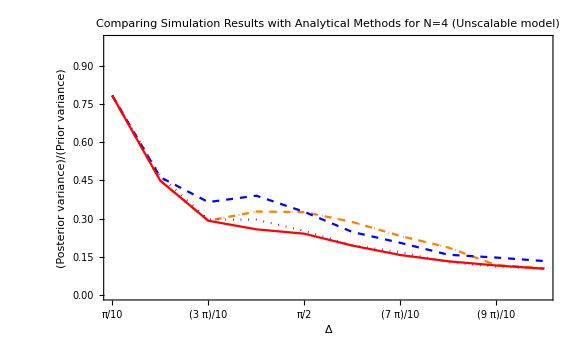

```mathematica
(*Needs to be 0.29662564242447337*)
```

```mathematica
(*(*Normalization term depending on the measurement outcome?*)
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
NormalizationTerm=∏_(i=1)^2 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
NormalizedBMSE = NormalizationTerm*BMSE/.AptStates;*)
```

#### Compare plots for N=4

```mathematica
MCA=MCAVaryΔ
```

{0.791559,0.446835,0.312248,0.287299,0.206233,0.134921,0.0910083,0.0672826,0.0779839,0.0485061}

```mathematica
MCA={0.7750201854703866,0.4942465681238499,0.3374615958772505,0.3452534692001444,0.2860898224128942,0.25007547813932435,0.17765369341379555,0.13153606847444343,0.11785530468575152,0.11670880858745618}
```

{0.77502,0.494247,0.337462,0.345253,0.28609,0.250075,0.177654,0.131536,0.117855,0.116709}

```mathematica
MCSA = {0.7837398433677253,0.4536090556738001,0.2739163064796318,0.2350774296474307,0.17770750155811743,0.14374881829066774,0.12245895320127148,0.10885047118339157,0.1044535037354056,0.08868957807323821}
```

{0.78374,0.453609,0.273916,0.235077,0.177708,0.143749,0.122459,0.10885,0.104454,0.0886896}

```mathematica
AnalyticA ={0.0064547614446658005,0.015362265800969058,0.02195683309461405,0.03891112854467223,0.051797884035783205,0.057654995088268504,0.06771113094186494,0.06721691385172052,0.07441611403221542,0.0842613968600595}
```

{0.00645476,0.0153623,0.0219568,0.0389111,0.0517979,0.057655,0.0677111,0.0672169,0.0744161,0.0842614}

```mathematica
AnalyticA=Table[AnalyticA[[n]]/((n π/10)^2/12),{n,1,10}]
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
AnalyticSA ={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
OptimalSA = {0.7832548199808358,0.4490954551497609,0.29166028593618665,0.26058612809564585,0.2406540258448837,0.19393250958529862,0.1567902732388312,0.13218789349385024,0.11558869633632414,0.10285374254650627}
```

{0.783255,0.449095,0.29166,0.260586,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

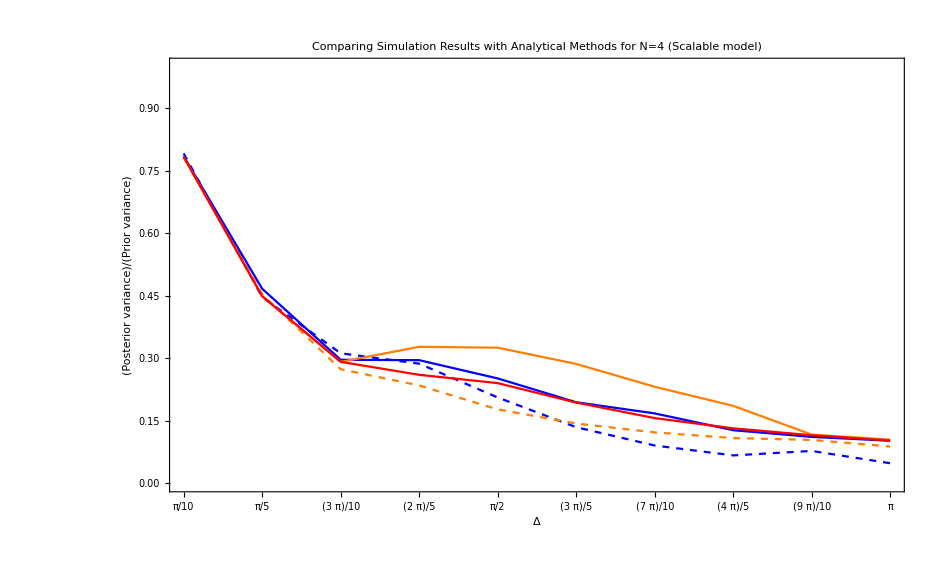

```mathematica
Show[ListLinePlot[MCA,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA"},{Right,Top}]],ListLinePlot[MCSA,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue},PlotLegends->Placed[{"Analytic Adaptive"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange},PlotLegends->Placed[{"Analytic Semi-Adaptive"},{Right,Top}]],ListLinePlot[OptimalSA,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Scalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize-> Large]
```

#### VarRatio MCSA, MCA with sbs optimal states plugged into global variance N=4, ns=2

```mathematica
(*Non-adaptive global*)
```

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
(*MonteCarlo Semi-Adaptive*)
```

```mathematica
MCSAPlugged={0.7832548199807943,0.44909545514972116,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.28673863672037136,0.23189593990295332,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*Semi-adaptive*)
```

```mathematica
AnalyticSA={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*MonteCarlo Adaptive 10 trials of 100 phitrue intervals (1000 total)*)
```

```mathematica
MCAPlugged10=MCAVaryΔ
```

{0.792134,0.479021,0.339269,0.263662,0.264563,0.182399,0.23943,0.0989743,0.0700832,0.0746591}

```mathematica
MCAPlugged100=MCAVaryΔ
```

{0.79585,0.465726,0.2893,0.276689,0.248536,0.183843,0.169411,0.10862,0.0881129,0.0772369}

```mathematica
MCAPlugged3=MCAVaryΔ
```

{0.798505,0.405386,0.225353,0.281024,0.263535,0.16197,0.157623,0.0834823,0.0734167,0.0614722}

```mathematica
(*Adaptive*)
```

```mathematica
AnalyticA ={0.7848048836429581,0.4669568863147173,0.29662564242447337,0.29568912007540094,0.2519147001923571,0.19472241150788455,0.16801400651733248,0.12769682385452574,0.11170264823418144,0.1024495735826159}
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

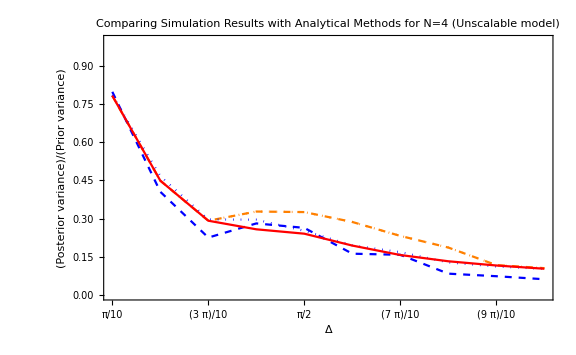

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged3,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

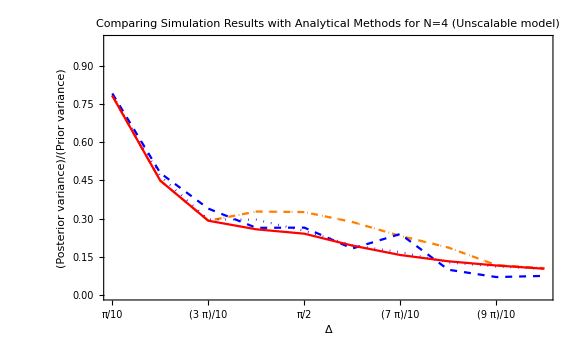

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged10,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 10 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

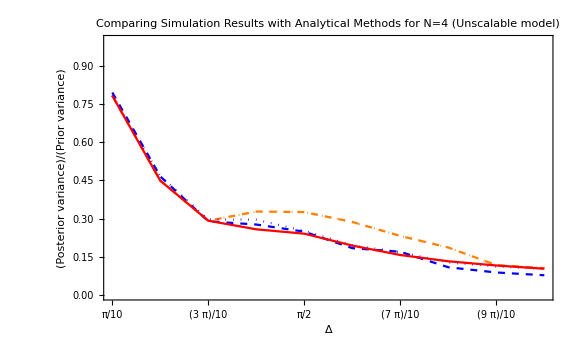

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged100,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 100 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged3,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

-Graphics-

## D. Error Analysis for 100 trials of 30 shots of N=3, Δinit=π

#### Error Analysis for 100 trials of 30 shots

```mathematica
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =π;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=30;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
Δnext
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,listOfPhaseEstimators},{phitrue,-1.5,1.5,0.3}];
```

```mathematica
{ntrial,nshots}
```

{100,30}

```mathematica
(*{ϕtrue, {{Δ,ϕ̃(after 100 shots for trial 1)} , {Δ,OverTilde[ϕ(after 100 shots for trial 2)]} ,...}}*)
```

```mathematica
MatrixForm[GridOfϕTrue]
```

(-1.5 | {{0.167073,-1.50807},{0.286202,-1.54655},{0.30896,-1.60556},{0.244883,-1.50077},{0.160712,-1.49962},{0.19396,-1.42878},{0.25605,-1.47329},{0.25605,-1.47329},{0.243105,-1.54192},{0.189767,-1.43629},{0.371124,-1.36025},{0.371124,-1.36025},{0.30896,-1.60556},{0.172096,-1.5259},{0.243105,-1.54192},{0.270225,-1.4395},{0.184236,-1.5571},{0.371124,-1.36025},{0.241567,-1.51471},{0.241567,-1.51471},{0.371124,-1.36025},{0.274245,-1.49436},{0.244883,-1.50077},{0.274245,-1.49436},{0.240728,-1.52849},{0.270225,-1.4395},{0.241567,-1.51471},{0.146673,-1.50745},{0.221852,-1.41618},{0.371124,-1.36025},{0.128072,-1.49434},{0.328327,-1.61968},{0.262739,-1.46022},{0.274245,-1.49436},{0.241567,-1.51471},{0.182246,-1.57549},{0.274245,-1.49436},{0.286202,-1.54655},{0.175629,-1.51688},{0.249928,-1.48689},{0.183612,-1.39878},{0.174975,-1.43802},{0.274245,-1.49436},{0.179193,-1.53199},{0.243105,-1.54192},{0.286202,-1.54655},{0.131024,-1.53923},{0.221572,-1.4129},{0.371124,-1.36025},{0.389864,-1.69581},{0.274245,-1.49436},{0.274245,-1.49436},{0.205888,-1.39831},{0.241567,-1.51471},{0.243105,-1.54192},{0.156185,-1.47505},{0.274245,-1.49436},{0.286202,-1.54655},{0.187824,-1.4202},{0.179216,-1.53844},{0.270225,-1.4395},{0.382677,-1.52701},{0.154418,-1.49549},{0.20854,0.554514},{0.371124,-1.36025},{0.199901,-1.47704},{0.25605,-1.47329},{0.207996,-1.47019},{0.179216,-1.53844},{0.286202,-1.54655},{0.156723,-1.49429},{0.194403,-1.49653},{0.169963,-1.46593},{0.183201,-1.42349},{0.170778,-1.42813},{0.192136,-1.56909},{0.36165,-1.55259},{0.134055,-1.52524},{0.371124,-1.36025},{0.290194,-1.59249},{0.241567,-1.51471},{0.177725,-1.51243},{0.169252,-1.54394},{0.12857,-1.50459},{0.286202,-1.54655},{0.244883,-1.50077},{0.196996,-1.48681},{0.262739,-1.46022},{0.209678,-1.39043},{0.187222,-1.47079},{0.158303,-1.43506},{0.142693,-1.43582},{0.270225,-1.4395},{0.150942,-1.47424},{0.24377,-1.39371},{0.244883,-1.50077},{0.286202,-1.54655},{0.249928,-1.48689},{0.346145,-1.60476},{0.407604,-1.54346}}
-1.2 | {{0.215868,-1.16902},{0.219132,-1.1528},{0.22769,-1.26721},{0.212604,-1.20997},{0.526961,-1.30359},{0.238735,-1.17487},{0.223231,-1.29574},{0.231444,-1.11985},{0.219127,-1.12371},{0.236812,-1.28982},{0.227817,-1.19247},{0.232453,-1.22457},{0.226028,-1.09776},{0.215078,-1.30155},{0.217367,-1.25253},{0.19661,-1.28787},{0.223679,-1.0771},{0.205796,-1.55613},{0.231316,-1.10568},{0.216781,-1.17645},{0.216122,-1.20205},{0.206813,-1.25868},{0.239132,-1.21909},{0.210113,-1.23389},{0.227837,-1.1192},{0.212715,-1.22196},{0.227355,-1.1498},{0.222338,-1.16755},{0.226008,-1.1848},{0.254457,-1.22841},{0.296953,-1.24727},{0.223376,-1.2725},{0.261841,-1.29958},{0.235818,-1.28262},{0.21805,-1.22405},{0.222607,-1.20648},{0.210681,-1.24811},{0.238377,-1.27379},{0.226414,-1.16772},{0.219516,-1.20413},{0.249508,-1.20161},{0.201408,-1.26825},{0.254467,-1.14036},{0.228033,-1.07431},{0.273528,-1.23942},{0.219323,-1.15415},{0.218327,-1.19407},{0.205459,-1.25605},{0.222952,-1.08511},{0.371124,-1.36025},{0.204244,-1.24824},{0.219133,-1.24126},{0.247018,-1.23973},{0.2272,-1.21556},{0.21115,-1.20869},{0.34264,-1.30117},{0.21445,-1.25533},{0.214109,-1.26622},{0.220443,-1.16988},{0.288459,-1.23061},{0.220174,-1.21636},{0.225058,-1.23338},{0.227625,-1.12459},{0.222974,-1.08402},{0.229219,-1.163},{0.208393,-1.23845},{0.224994,-1.19022},{0.202576,-1.27073},{0.222327,-1.16413},{0.354737,-1.17922},{0.216502,-1.26788},{0.218567,-1.16116},{0.22663,-1.19598},{0.222181,-1.09492},{1.16123,-1.63018},{0.218427,-1.26358},{0.215758,-1.14898},{0.212112,-1.19067},{0.221635,-1.1505},{0.23257,-1.23381},{0.230819,-1.23431},{0.223899,-1.13871},{0.243376,-1.33475},{0.240292,-1.26219},{0.228173,-1.12361},{0.225889,-1.12468},{0.228935,-1.07348},{0.230158,-1.23717},{0.472203,-1.52817},{0.217687,-1.29835},{0.265503,-1.10534},{0.234244,-1.21024},{0.210164,-1.25344},{0.233786,-1.21597},{0.205504,-1.23862},{0.233379,-1.23365},{0.235309,-1.18081},{0.241753,-1.18581},{0.221175,-1.24903},{0.214956,-1.19338}}
-0.9 | {{0.265996,-0.841826},{0.259674,-0.862778},{0.269709,-0.806172},{0.2188,-0.880608},{0.211703,-0.861929},{0.321348,-0.733602},{0.249548,-0.851134},{0.236087,-0.924065},{0.215904,-0.853643},{0.218427,-0.974196},{0.226233,-0.970417},{0.256498,-0.872853},{0.245311,-0.991471},{0.200066,-0.787998},{0.272103,-0.880129},{0.223319,-0.866025},{0.297965,-0.808879},{0.225822,-0.936331},{0.223956,-0.869279},{0.214663,-0.853729},{0.219124,-0.901912},{0.245658,-0.965419},{0.215189,-0.86118},{0.226119,-0.980804},{0.221197,-0.905429},{0.223886,-0.888938},{0.2283,-0.992668},{0.63245,-0.774487},{0.243404,-0.923988},{0.211582,-0.910273},{0.578375,-0.957693},{0.308914,-0.975853},{0.250443,-0.903975},{0.224236,-0.938936},{0.247621,-0.767554},{0.233675,-0.989435},{0.221644,-0.924897},{1.64561,-1.57084},{0.230447,-1.06273},{0.210221,-0.905338},{0.219779,-0.92904},{0.197299,-0.847012},{0.222675,-0.940796},{0.274276,-0.815701},{0.20969,-0.902531},{0.241656,-0.894481},{0.211944,-0.865654},{0.210559,-0.881506},{0.240973,-0.859787},{0.218809,-0.918114},{0.220235,-0.819284},{0.21603,-0.844847},{0.243987,-0.874307},{0.227956,-0.959545},{0.237201,-1.00318},{0.274831,-0.901735},{0.340278,-0.965551},{0.413161,-0.500445},{0.220026,-0.934418},{0.211151,-0.84363},{0.225592,-0.927419},{0.223685,-0.951018},{0.227206,-0.940501},{0.22326,-0.909427},{0.227384,-0.934335},{0.231933,-0.940227},{0.290523,-0.988269},{0.22149,-0.931522},{0.224318,-0.812039},{0.220401,-0.836599},{0.276016,-0.823291},{0.219641,-0.809654},{0.202232,-0.85046},{0.215959,-0.771986},{0.223312,-1.03778},{0.222158,-0.854302},{0.261945,-0.881954},{0.204177,-0.824138},{0.365244,-0.842928},{0.270416,-0.965218},{0.267394,-0.783837},{0.226472,-0.902278},{0.250818,-0.819762},{0.233891,-0.993138},{0.213496,-0.852537},{0.222248,-0.783243},{0.205691,-0.850105},{0.247309,-0.78752},{0.217711,-0.880078},{0.332064,-0.772469},{0.229718,-0.854357},{0.221323,-0.854676},{0.208664,-0.861344},{0.239083,-0.924842},{0.215965,-0.917973},{0.273563,-0.990478},{0.362654,-0.917563},{0.211207,-0.840331},{0.215623,-0.883949},{0.243291,-0.848843}}
-0.6 | {{0.229403,-0.591342},{0.26347,-0.537543},{0.212785,-0.528896},{0.177664,-0.526814},{0.289104,-0.572218},{0.309371,-0.537316},{0.215513,-0.612849},{0.284998,-0.608259},{0.252192,-0.662089},{0.225556,-0.317},{0.245702,-0.692021},{0.363767,-0.629228},{0.185365,-0.615658},{0.183751,-0.564019},{0.119943,-0.604618},{0.34628,-0.551935},{0.298105,-0.489635},{0.226034,-0.566417},{0.178299,-0.484344},{0.160884,-0.522305},{0.226258,-0.545754},{0.359517,-0.577425},{0.26333,-0.587605},{0.201872,-0.626072},{0.257063,-0.544672},{0.211229,-0.665447},{0.130235,-0.489517},{0.108255,-0.530134},{0.165116,-0.513225},{0.189197,-0.684725},{0.178559,-0.719945},{0.142922,-0.48663},{0.2504,-0.575732},{0.305088,-0.550326},{0.311103,-0.483068},{0.174366,-0.636621},{0.243556,-0.628764},{0.209388,-0.652834},{0.355313,-0.553744},{0.22482,-0.617372},{0.182876,-0.647604},{0.249146,-0.640594},{0.311103,-0.483068},{0.249229,-0.543895},{0.256761,-0.697194},{0.326368,-0.741056},{0.282559,-0.515389},{0.49389,-0.431402},{0.160992,-0.490916},{0.371637,-0.611702},{0.208585,-0.546865},{0.389086,-0.679065},{0.178483,-0.474673},{0.175149,-0.56765},{0.205446,-0.619643},{0.333101,-0.572898},{0.278766,-0.604178},{0.289104,-0.572218},{0.138246,-0.568087},{0.204077,-0.605112},{0.231967,-0.542666},{0.345355,-0.484441},{0.19534,-0.575721},{5.29218,-1.57078},{0.257063,-0.544672},{0.440799,-0.597064},{0.366604,-0.470567},{0.249146,-0.640594},{0.250414,-0.450716},{0.233357,-0.603975},{0.114779,-0.479613},{0.131315,-0.555488},{0.281959,-0.626317},{0.254763,-0.651864},{0.229403,-0.591342},{0.216391,-0.679701},{0.268861,-0.566547},{0.261248,-0.540493},{0.20854,-0.554514},{0.289104,-0.572218},{0.236267,-0.556662},{0.310803,-0.49153},{0.260269,-0.662469},{0.267597,-0.709113},{0.167894,-0.557954},{0.371943,-0.567467},{0.294326,-0.580113},{0.280319,-0.538118},{0.252192,-0.662089},{0.312209,-0.556801},{0.191084,-0.660675},{0.27647,-0.49694},{0.152339,-0.588163},{0.112177,-0.523168},{0.15196,-0.523713},{0.406013,-0.492209},{0.316231,-0.610257},{0.226034,-0.566417},{0.220456,-0.535111},{0.389133,-0.60128}}
-0.3 | {{0.23874,-0.278144},{0.265252,-0.288907},{0.230739,-0.316157},{0.190252,-0.297736},{0.2157,-0.311997},{0.19734,-0.257516},{0.229536,-0.249674},{0.209197,-0.388648},{0.244158,-0.214196},{0.211867,-0.229295},{0.260476,-0.310181},{0.197593,-0.260432},{0.185737,-0.364331},{0.372201,-0.570851},{0.253619,-0.269308},{0.216332,-0.229879},{0.262212,-0.238831},{0.177366,-0.376611},{0.220066,-0.226909},{0.224669,-0.139193},{0.186773,-0.284148},{0.219835,-0.183562},{0.182389,-0.344507},{0.213766,-0.323507},{0.209591,-0.288391},{0.449906,-0.475913},{0.251795,-0.376356},{0.175217,-0.320818},{0.269795,-0.40631},{0.376791,-0.293199},{0.269795,-0.40631},{0.243084,-0.328861},{0.198274,-0.330877},{0.258558,-0.236415},{0.174473,-0.425827},{0.211598,-0.25767},{0.304986,-0.208814},{0.351282,-0.238075},{0.203402,-0.262925},{0.298595,-0.358192},{0.200888,-0.294408},{0.263033,-0.301196},{0.253227,-0.334153},{0.248037,-0.339222},{0.205365,-0.360131},{0.430557,-0.287654},{0.193443,-0.251783},{0.299341,-0.423672},{0.193087,-0.216667},{0.183109,-0.362626},{0.231198,-0.41417},{0.339974,-0.156562},{0.229122,-0.297764},{0.284409,-0.310316},{0.307484,-0.538319},{0.18935,-0.353147},{0.36372,-0.371519},{0.274705,-0.128596},{0.228003,-0.283316},{0.260092,-0.355585},{0.188861,-0.358088},{0.20885,-0.277246},{0.298595,-0.358192},{0.302685,-0.136027},{0.198006,-0.357425},{0.376791,-0.293199},{0.232628,-0.329583},{0.216029,-0.205174},{0.216364,-0.24881},{0.255074,-0.268813},{0.199272,-0.324764},{0.214502,-0.239592},{0.292414,1.71237},{0.199832,-0.320113},{0.302348,-0.285259},{0.260092,-0.355585},{0.20206,-0.224946},{0.218631,-0.303585},{0.298595,-0.358192},{0.302348,-0.285259},{0.298595,-0.358192},{0.302348,-0.285259},{0.309609,-0.248152},{0.199341,-0.274123},{0.260476,-0.310181},{0.314529,-0.364321},{0.376791,-0.293199},{0.194159,-0.274873},{0.298595,-0.358192},{0.184023,-0.325798},{0.277184,-0.385196},{0.216212,-0.368034},{0.19797,-0.218302},{0.23614,-0.324787},{0.235464,-0.22303},{0.196591,-0.377693},{0.196925,-0.363205},{0.251907,-0.351661},{0.211015,-0.207588},{0.208108,-0.351081}}
0. | {{0.223541,0.0199169},{0.223022,-0.088117},{0.220047,-0.0984171},{0.761225,-1.76109},{0.223335,0.0253822},{0.269813,-0.066431},{0.221879,-0.0336349},{0.223965,-0.0318723},{0.223432,0.00658586},{0.222806,-0.0157261},{0.249943,-0.0887969},{0.223577,0.0166752},{0.252999,0.0295},{0.22685,-0.00248739},{0.22942,-0.0181038},{0.736451,-0.294606},{3.56791,1.56981},{0.225281,-0.0468623},{0.223466,-0.00599676},{0.225445,0.0426792},{0.226598,-0.0869428},{4.8966,-1.59692},{0.228303,0.0582761},{0.22727,-0.0356679},{0.219258,0.0877536},{0.409995,0.00745403},{0.223841,0.0508289},{0.222992,0.00423807},{0.223009,0.00528007},{0.222675,0.0146874},{0.229355,-0.00173639},{0.22928,-0.0679563},{0.242359,0.0765705},{0.229116,0.0846516},{0.402753,0.174731},{0.222406,-0.0278642},{0.223711,0.00489109},{0.224612,0.0646089},{0.223229,-0.080887},{0.435049,0.190484},{0.22323,-0.0432494},{0.438889,-0.178965},{0.223233,0.0044135},{0.22724,0.0230013},{0.223876,-0.0254566},{0.223829,-0.00535181},{0.221279,0.0497854},{0.221512,-0.0477156},{0.225185,-0.0343858},{0.267616,0.0755849},{0.218234,0.0859129},{0.290848,-0.182487},{0.222564,-0.0236445},{0.231001,-0.00892486},{0.222103,-0.0277221},{0.218608,0.111352},{0.221722,-0.0582938},{0.235872,-0.0585637},{0.986448,0.484981},{0.223086,0.0226567},{0.227084,-0.0292748},{0.221733,-0.165625},{4.23317,1.64651},{1.73723,0.525237},{0.223827,-0.0762862},{0.223434,-0.00722198},{0.286479,0.530492},{0.284676,0.173433},{0.516523,-0.050918},{0.218283,0.084301},{0.223739,0.102129},{0.225408,0.0298506},{0.235121,0.105729},{0.223296,0.0118552},{0.223723,-0.0641327},{0.220523,0.072484},{0.22695,-0.171098},{0.228733,0.0218534},{0.223713,0.0340359},{0.254778,0.0895201},{0.279583,0.11995},{0.297241,0.148787},{0.225328,-0.048522},{0.228741,0.0419546},{0.2211,0.0653872},{0.22833,0.102429},{0.224383,-0.0481527},{0.223244,0.0182969},{0.223085,0.0803561},{0.226842,0.00135778},{0.223871,0.0656656},{0.245223,-0.106986},{0.26372,0.0220177},{0.222275,-0.0224628},{0.224985,0.0884703},{0.225888,-0.0190166},{0.223464,-0.0125215},{0.224104,0.000263139},{0.226729,-0.0152718},{0.221612,0.0432651}}
0.3 | {{0.237222,0.242399},{5.08961,1.57397},{0.180432,0.357986},{0.21682,0.238833},{0.243851,0.209961},{0.250394,0.279566},{0.405532,-1.80261},{0.223309,0.279841},{0.200741,0.36092},{0.320354,0.151224},{0.216643,0.329779},{0.189998,0.363611},{0.258647,0.405334},{0.188491,0.351746},{0.234575,0.24801},{0.376791,0.293199},{0.222389,0.220287},{0.169889,0.34591},{0.262564,0.233744},{0.23904,0.392469},{0.370575,0.3178},{0.376791,0.293199},{0.213931,0.261219},{0.416472,0.461937},{0.247087,0.255756},{0.298595,0.358192},{0.251038,0.452807},{0.211459,0.286064},{0.235131,0.229077},{0.367667,0.194805},{0.309609,0.248152},{0.577357,0.418402},{0.202624,0.224144},{0.178685,0.340055},{0.222435,0.158047},{0.347437,0.417965},{0.217492,0.267912},{0.212377,0.319169},{0.219869,0.367079},{0.263033,0.301196},{0.190514,0.346511},{0.244846,0.361431},{0.274059,0.26573},{0.200616,0.273879},{0.322589,0.315513},{0.299341,0.423672},{0.188712,0.309999},{0.314529,0.364321},{0.299341,0.423672},{0.299341,0.423672},{0.219315,0.267287},{0.255573,0.334758},{0.253074,0.346565},{0.252772,0.348668},{0.210714,0.266653},{0.291752,0.31035},{0.309609,0.248152},{0.24153,0.260587},{0.245641,0.135258},{0.403278,-1.74719},{0.221983,0.326838},{0.217805,0.299943},{0.198361,0.265926},{0.376791,0.293199},{0.151734,0.490382},{0.230203,0.249799},{0.22949,0.367332},{0.207798,0.220937},{0.240596,0.319825},{0.310166,-1.76726},{0.241954,0.257603},{0.330243,0.464757},{0.232204,0.326061},{0.179369,0.35867},{0.230207,0.308201},{0.201301,0.293719},{0.32478,-1.79101},{0.314529,0.364321},{0.406238,-1.56916},{0.370575,0.3178},{0.210834,0.28979},{0.255257,0.265766},{0.445767,0.466716},{0.178866,0.35598},{0.219156,0.263728},{0.195369,0.333991},{0.33544,-1.83079},{0.186707,0.38401},{0.313374,0.401864},{0.235327,0.382551},{0.19883,0.331016},{0.247331,0.282738},{0.386138,0.537202},{0.205695,0.259666},{0.370856,0.289668},{0.241228,0.302934},{0.227892,0.324683},{0.175476,0.301917},{0.248975,0.281182},{0.376791,0.293199}}
0.6 | {{0.215066,0.639632},{0.410798,0.537418},{0.400423,0.402813},{0.342056,0.747031},{0.252281,0.56872},{0.138422,0.501894},{0.342056,0.747031},{0.241419,0.54697},{0.206137,0.522687},{0.436651,0.720801},{0.197491,0.660297},{0.220672,0.737719},{0.406242,0.691948},{0.203723,0.620109},{0.204963,0.59096},{0.258079,0.525732},{0.313332,0.670447},{0.16901,0.512332},{0.220474,0.546631},{0.250157,0.709726},{0.318549,0.535101},{0.261248,0.540493},{0.200777,0.608721},{0.314907,0.566226},{0.223217,0.634642},{0.410912,0.535913},{0.363767,0.629228},{0.311103,0.483068},{0.17982,0.526989},{0.162219,0.565958},{0.154678,0.647144},{0.18261,0.615154},{0.278766,0.604178},{0.286335,0.616261},{0.21445,0.550407},{0.223412,0.686324},{0.249229,0.543895},{0.347726,0.556772},{0.287004,0.538694},{0.363767,0.629228},{3.14424,1.5708},{0.184732,0.686747},{0.241031,0.67374},{0.248932,0.628801},{0.189759,0.614794},{0.177555,0.51728},{0.249229,0.543895},{0.257736,0.608165},{0.261248,0.540493},{0.170491,0.526494},{0.275018,0.527755},{0.216391,0.679701},{0.22647,0.552905},{0.170477,0.650888},{0.310478,0.561319},{0.210405,0.547539},{0.239256,0.531261},{0.282981,0.56654},{0.173741,0.584664},{0.220338,0.554069},{0.231243,0.509157},{0.353377,0.590987},{0.328352,0.630688},{0.345711,0.528019},{0.376721,0.577739},{0.23567,0.54239},{0.344926,0.590174},{0.254763,0.651864},{0.252192,0.662089},{0.257289,-1.50852},{0.281959,0.626317},{0.215066,0.639632},{0.187671,0.52042},{0.342056,0.747031},{0.234299,0.723028},{0.12093,0.547476},{0.353377,0.590987},{0.274278,0.664748},{0.281959,0.626317},{0.252281,0.56872},{0.216805,0.726722},{0.356961,0.564487},{0.245127,0.519076},{0.225984,0.688423},{0.220456,0.535111},{0.348302,0.571659},{0.210643,0.738926},{0.252281,0.56872},{0.325153,0.502465},{0.263047,0.620309},{0.190924,0.618355},{0.189091,0.551911},{0.23588,0.54},{0.24839,0.484082},{0.316231,0.610257},{0.220778,0.540803},{0.185765,0.680668},{0.363767,0.629228},{0.280287,0.474342},{2.27512,1.5708}}
0.9 | {{0.219748,0.869601},{0.231452,0.844452},{0.214022,0.534233},{0.20825,0.762848},{0.233858,0.857357},{0.256761,0.697194},{0.221529,0.98411},{0.230409,0.878466},{0.2248,0.902756},{0.233369,0.958811},{0.228439,0.865132},{0.223359,0.89272},{0.226045,0.849627},{0.321731,0.944187},{0.241303,0.944404},{0.216569,0.893589},{0.229271,0.827036},{0.316711,0.805674},{0.284459,1.02193},{0.33121,0.939364},{0.263766,0.775199},{0.26281,0.89435},{0.253211,0.871786},{0.224395,0.951092},{0.251518,0.846633},{0.246965,0.995723},{0.296893,0.902668},{0.21734,0.909498},{0.237833,0.996751},{0.214825,0.800363},{0.208721,0.849176},{0.230632,0.99331},{0.25852,0.823419},{0.238656,0.957102},{0.231967,1.03257},{0.222781,0.967991},{0.280989,0.772023},{0.229256,0.867233},{0.207802,0.853754},{0.244461,0.892721},{0.21527,0.896808},{0.225319,0.99922},{0.245692,0.871631},{0.213365,0.872493},{0.271511,0.836826},{0.231583,0.945302},{0.216336,0.955837},{0.214281,0.871917},{0.22057,0.92438},{0.222531,0.89416},{0.227349,0.960418},{0.228701,0.998236},{0.205129,0.877192},{0.216056,0.796867},{0.457578,0.563519},{0.237109,0.832707},{0.226087,0.835832},{0.206247,0.876697},{0.239242,0.802146},{0.226567,0.918277},{0.221307,0.89937},{0.220425,0.887706},{0.245932,0.929329},{0.217926,0.951773},{0.270332,0.87791},{0.240734,0.842624},{0.233904,0.851744},{0.227451,0.983104},{0.240923,0.809907},{0.208951,0.894567},{0.217855,0.97351},{0.23112,1.036},{0.225502,0.909691},{0.242527,0.916605},{0.239155,0.900832},{0.212129,0.793015},{0.318968,0.836477},{0.204228,0.825846},{0.235179,0.94316},{0.211362,0.879416},{0.225385,0.950945},{0.208241,0.824345},{0.230163,1.02788},{0.212168,0.912834},{0.217876,0.977353},{0.215262,0.832418},{0.223748,1.01733},{0.212032,0.871427},{0.229122,0.868157},{0.215064,0.864421},{1.08293,0.587568},{0.279296,0.892819},{0.220305,0.937152},{0.229931,0.826868},{0.262553,0.87655},{0.229609,0.782469},{0.220538,0.930123},{0.254214,0.876792},{0.220218,0.924304},{0.214309,0.859874}}
1.2 | {{0.239729,1.1619},{0.232167,1.14178},{0.204512,1.30083},{0.21277,1.1718},{0.21079,1.21802},{0.197639,1.27111},{0.220287,1.19466},{0.24414,1.15668},{0.21822,1.13291},{0.217419,1.22419},{0.217668,1.13765},{0.220912,1.09553},{0.558718,1.09966},{0.205063,1.21745},{0.230058,1.24307},{0.218892,1.16336},{0.222525,1.25315},{0.208268,1.19689},{0.226143,1.28086},{0.220383,1.20806},{0.21561,1.16303},{0.246493,1.11359},{0.295022,1.33001},{0.482696,1.18327},{0.210663,1.24486},{0.223388,1.13546},{0.200397,1.26994},{0.250628,1.31932},{0.235709,1.19844},{0.231252,1.19196},{0.224194,1.2261},{0.229881,1.19313},{0.208245,1.23155},{0.220631,1.16846},{0.205943,1.22549},{0.22789,1.15501},{0.209208,1.23184},{0.247769,1.19401},{0.24102,1.23982},{0.209427,1.22178},{0.239135,1.34651},{0.230632,1.19453},{0.243764,1.09962},{0.209291,1.25301},{0.221015,1.15857},{0.236259,1.27319},{0.213448,1.27091},{0.226601,1.1093},{0.231059,1.18876},{0.204029,1.26967},{0.220234,1.14232},{0.232085,1.30964},{0.216761,1.16042},{0.249835,1.24675},{0.228883,1.12062},{0.210746,1.27231},{0.579799,-0.555477},{0.291882,1.24103},{0.910508,1.49292},{0.44444,1.03964},{0.218643,1.27677},{0.222136,1.13322},{0.222151,1.21687},{0.246899,1.21979},{0.220993,1.2223},{0.273799,1.12989},{0.233769,1.24979},{0.493213,1.15245},{0.199324,1.35397},{0.217485,1.22881},{0.219013,1.22596},{0.234048,1.17295},{0.213831,1.15853},{0.242775,1.1241},{0.254536,1.20481},{0.212316,1.1728},{0.23531,1.2021},{0.239789,1.19397},{0.219292,1.27937},{0.235874,1.17395},{0.216906,1.23382},{0.225392,1.19229},{0.222594,1.09226},{0.229757,1.19178},{0.206022,1.23569},{0.222815,1.2526},{0.25575,1.22712},{0.215194,1.19181},{0.212239,1.23663},{0.229784,1.22268},{0.215482,-0.845682},{0.298119,1.12228},{0.233167,1.15477},{0.236717,1.2843},{0.893252,1.39884},{0.245331,1.05443},{0.291724,1.21402},{0.229443,1.19689},{0.211439,1.27143},{0.273528,1.23942}}
1.5 | {{0.18593,1.37191},{0.264862,1.60806},{0.172297,1.5061},{0.260386,1.54738},{0.30896,1.60556},{0.371124,1.36025},{0.245978,1.40923},{0.25605,1.47329},{0.371124,1.36025},{0.262739,1.46022},{0.244883,1.50077},{0.371124,1.36025},{0.259422,1.56755},{0.243105,1.54192},{0.243105,1.54192},{0.25605,1.47329},{0.286202,1.54655},{0.262739,1.46022},{0.243105,1.54192},{0.170884,1.55272},{0.170661,1.51239},{0.371124,1.36025},{0.169899,1.41675},{0.249265,1.55492},{0.302947,1.5808},{0.192595,1.48524},{0.133862,1.47046},{0.262739,1.46022},{0.226685,1.35465},{0.204049,1.41925},{0.274245,1.49436},{0.240728,1.52849},{0.38649,1.52177},{0.152635,1.49791},{0.397981,1.51116},{0.178144,1.38258},{0.172096,1.5259},{0.230076,1.33065},{0.274245,1.49436},{0.239572,-0.635119},{0.169768,1.54836},{0.271216,1.37799},{0.177725,1.51243},{0.196996,1.48681},{0.249265,1.55492},{0.189004,1.38215},{0.240728,1.52849},{0.240728,1.52849},{0.271216,1.37799},{0.19,1.52481},{0.371124,1.36025},{0.209745,1.38706},{0.193511,1.4016},{0.270225,1.4395},{0.193238,1.3805},{0.244883,1.50077},{0.192488,1.43085},{0.174621,1.44311},{0.328327,1.61968},{0.249928,1.48689},{0.19,1.52481},{0.134013,1.53047},{0.249265,1.55492},{0.290194,1.59249},{0.273312,1.57996},{0.170769,1.53043},{0.163528,1.43072},{0.243105,1.54192},{0.364753,1.54229},{0.206726,1.45439},{0.274245,1.49436},{0.371124,1.36025},{0.290194,1.59249},{0.259422,1.56755},{0.133369,1.51762},{0.176195,1.49344},{0.187222,1.47079},{0.259422,1.56755},{0.215613,1.58936},{0.241567,1.51471},{0.169919,1.47174},{0.192264,1.50614},{0.274245,1.49436},{0.273312,1.57996},{0.135189,1.49289},{0.249928,1.48689},{0.286202,1.54655},{0.290194,1.59249},{0.371124,1.36025},{0.241567,1.51471},{0.147936,1.47536},{0.274245,1.49436},{0.25605,1.47329},{0.170661,1.51239},{0.162787,1.43168},{0.30896,1.60556},{0.290194,1.59249},{0.162717,1.4602},{0.347163,1.60398},{0.198626,1.42083}})

```mathematica
(*Mean of phase estimators over 100 trials*)
```

```mathematica
listOfMeanϕs=Table[{GridOfϕTrue[[m,1]],Mean[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.46966},{-1.2,-1.21764},{-0.9,-0.891834},{-0.6,-0.582769},{-0.3,-0.286306},{0.,0.0163596},{0.3,0.204443},{0.6,0.592487},{0.9,0.883415},{1.2,1.17001},{1.5,1.46896}}

```mathematica
(*Median of phase estimators over 10 trials - less effect of outliers*)
```

```mathematica
listOfMedianϕs=Table[{GridOfϕTrue[[m,1]],Median[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.49436},{-1.2,-1.21617},{-0.9,-0.88173},{-0.6,-0.567869},{-0.3,-0.30239},{0.,0.00465229},{0.3,0.302425},{0.6,0.581201},{0.9,0.883561},{1.2,1.20346},{1.5,1.49614}}

```mathematica
(*Squared error (SE) of the phase estimators from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfSEs=Table[Table[{GridOfϕTrue[[m,1]],(GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]])^2},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0000651947},{-1.5,0.00216728},{-1.5,0.0111426},{-1.5,5.98248×10^-7},{-1.5,1.42184×10^-7},{-1.5,0.00507217},{-1.5,0.000713274},{-1.5,0.000713274},{-1.5,0.00175695},{-1.5,0.00405873},{-1.5,0.0195308},{-1.5,0.0195308},{-1.5,0.0111426},{-1.5,0.000670591},{-1.5,0.00175695},{-1.5,0.00365993},{-1.5,0.00326031},{-1.5,0.0195308},{-1.5,0.000216524},{-1.5,0.000216524},{-1.5,0.0195308},{-1.5,0.0000317594},{-1.5,5.98248×10^-7},{-1.5,0.0000317594},{-1.5,0.000811452},{-1.5,0.00365993},{-1.5,0.000216524},{-1.5,0.0000555511},{-1.5,0.00702604},{-1.5,0.0195308},{-1.5,0.0000320881},{-1.5,0.0143238},{-1.5,0.00158248},{-1.5,0.0000317594},{-1.5,0.000216524},{-1.5,0.00569945},{-1.5,0.0000317594},{-1.5,0.00216728},{-1.5,0.000284843},{-1.5,0.000171974},{-1.5,0.0102452},{-1.5,0.00384103},{-1.5,0.0000317594},{-1.5,0.00102321},{-1.5,0.00175695},{-1.5,0.00216728},{-1.5,0.00153917},{-1.5,0.00758654},{-1.5,0.0195308},{-1.5,0.0383415},{-1.5,0.0000317594},{-1.5,0.0000317594},{-1.5,0.0103415},{-1.5,0.000216524},{-1.5,0.00175695},{-1.5,0.000622289},{-1.5,0.0000317594},{-1.5,0.00216728},{-1.5,0.00636763},{-1.5,0.00147788},{-1.5,0.00365993},{-1.5,0.000729396},{-1.5,0.0000203573},{-1.5,4.22103},{-1.5,0.0195308},{-1.5,0.000527183},{-1.5,0.000713274},{-1.5,0.000888747},{-1.5,0.00147788},{-1.5,0.00216728},{-1.5,0.0000326546},{-1.5,0.0000120075},{-1.5,0.00116084},{-1.5,0.00585412},{-1.5,0.00516539},{-1.5,0.00477337},{-1.5,0.00276559},{-1.5,0.000637125},{-1.5,0.0195308},{-1.5,0.0085542},{-1.5,0.000216524},{-1.5,0.00015462},{-1.5,0.00193108},{-1.5,0.0000210275},{-1.5,0.00216728},{-1.5,5.98248×10^-7},{-1.5,0.000173928},{-1.5,0.00158248},{-1.5,0.0120064},{-1.5,0.000853082},{-1.5,0.00421673},{-1.5,0.00411912},{-1.5,0.00365993},{-1.5,0.000663367},{-1.5,0.0112969},{-1.5,5.98248×10^-7},{-1.5,0.00216728},{-1.5,0.000171974},{-1.5,0.0109749},{-1.5,0.00188869}},{{-1.2,0.000960041},{-1.2,0.00222823},{-1.2,0.00451765},{-1.2,0.0000994987},{-1.2,0.0107317},{-1.2,0.000631438},{-1.2,0.00916666},{-1.2,0.00642422},{-1.2,0.00582016},{-1.2,0.00806698},{-1.2,0.0000567348},{-1.2,0.000603506},{-1.2,0.0104522},{-1.2,0.0103114},{-1.2,0.00275902},{-1.2,0.00772042},{-1.2,0.0151053},{-1.2,0.126826},{-1.2,0.00889624},{-1.2,0.000554648},{-1.2,4.22182×10^-6},{-1.2,0.00344313},{-1.2,0.000364287},{-1.2,0.00114844},{-1.2,0.00652897},{-1.2,0.000482405},{-1.2,0.00251961},{-1.2,0.00105298},{-1.2,0.000231055},{-1.2,0.000807034},{-1.2,0.00223479},{-1.2,0.00525688},{-1.2,0.00991682},{-1.2,0.00682578},{-1.2,0.000578189},{-1.2,0.0000419775},{-1.2,0.00231445},{-1.2,0.0054455},{-1.2,0.00104201},{-1.2,0.0000170458},{-1.2,2.58684×10^-6},{-1.2,0.00465848},{-1.2,0.00355641},{-1.2,0.0157981},{-1.2,0.00155425},{-1.2,0.00210242},{-1.2,0.0000351871},{-1.2,0.00314202},{-1.2,0.0132005},{-1.2,0.0256792},{-1.2,0.0023267},{-1.2,0.00170206},{-1.2,0.00157871},{-1.2,0.000241973},{-1.2,0.0000754333},{-1.2,0.0102359},{-1.2,0.00306175},{-1.2,0.00438454},{-1.2,0.000906995},{-1.2,0.000936939},{-1.2,0.000267499},{-1.2,0.00111438},{-1.2,0.00568641},{-1.2,0.0134525},{-1.2,0.00136927},{-1.2,0.00147844},{-1.2,0.0000956485},{-1.2,0.00500312},{-1.2,0.00128658},{-1.2,0.000431623},{-1.2,0.00460766},{-1.2,0.00150871},{-1.2,0.0000161359},{-1.2,0.0110417},{-1.2,0.185052},{-1.2,0.00404214},{-1.2,0.00260337},{-1.2,0.0000869814},{-1.2,0.00245023},{-1.2,0.00114321},{-1.2,0.00117749},{-1.2,0.00375674},{-1.2,0.0181582},{-1.2,0.00386793},{-1.2,0.00583531},{-1.2,0.00567272},{-1.2,0.0160066},{-1.2,0.00138151},{-1.2,0.107698},{-1.2,0.00967362},{-1.2,0.00896082},{-1.2,0.000104904},{-1.2,0.00285583},{-1.2,0.000255189},{-1.2,0.00149125},{-1.2,0.00113253},{-1.2,0.000368278},{-1.2,0.000201478},{-1.2,0.0024041},{-1.2,0.0000438035}},{{-0.9,0.00338417},{-0.9,0.00138549},{-0.9,0.00880374},{-0.9,0.000376048},{-0.9,0.00144943},{-0.9,0.0276884},{-0.9,0.0023879},{-0.9,0.000579109},{-0.9,0.00214897},{-0.9,0.00550505},{-0.9,0.00495852},{-0.9,0.000736976},{-0.9,0.0083669},{-0.9,0.0125446},{-0.9,0.000394842},{-0.9,0.00115433},{-0.9,0.00830312},{-0.9,0.00131997},{-0.9,0.000943765},{-0.9,0.00214103},{-0.9,3.65622×10^-6},{-0.9,0.0042797},{-0.9,0.00150698},{-0.9,0.00652932},{-0.9,0.0000294733},{-0.9,0.000122363},{-0.9,0.00858741},{-0.9,0.0157536},{-0.9,0.000575445},{-0.9,0.000105541},{-0.9,0.00332853},{-0.9,0.00575368},{-0.9,0.0000158002},{-0.9,0.00151598},{-0.9,0.0175421},{-0.9,0.00799868},{-0.9,0.000619857},{-0.9,0.450022},{-0.9,0.0264802},{-0.9,0.0000284953},{-0.9,0.000843342},{-0.9,0.0028077},{-0.9,0.00166428},{-0.9,0.00710634},{-0.9,6.4063×10^-6},{-0.9,0.0000304617},{-0.9,0.00117967},{-0.9,0.000342035},{-0.9,0.00161705},{-0.9,0.000328125},{-0.9,0.00651515},{-0.9,0.00304184},{-0.9,0.000660134},{-0.9,0.00354562},{-0.9,0.0106467},{-0.9,3.01188×10^-6},{-0.9,0.00429696},{-0.9,0.159644},{-0.9,0.00118457},{-0.9,0.00317755},{-0.9,0.000751806},{-0.9,0.00260286},{-0.9,0.0016403},{-0.9,0.0000888667},{-0.9,0.00117887},{-0.9,0.00161821},{-0.9,0.00779141},{-0.9,0.000993657},{-0.9,0.00773706},{-0.9,0.00401973},{-0.9,0.00588425},{-0.9,0.00816236},{-0.9,0.00245417},{-0.9,0.0163875},{-0.9,0.0189833},{-0.9,0.00208826},{-0.9,0.000325674},{-0.9,0.00575503},{-0.9,0.00325722},{-0.9,0.00425332},{-0.9,0.0134938},{-0.9,5.19145×10^-6},{-0.9,0.00643819},{-0.9,0.00867466},{-0.9,0.00225272},{-0.9,0.0136321},{-0.9,0.00248954},{-0.9,0.0126517},{-0.9,0.000396898},{-0.9,0.0162641},{-0.9,0.00208328},{-0.9,0.00205429},{-0.9,0.00149425},{-0.9,0.000617123},{-0.9,0.000323037},{-0.9,0.00818632},{-0.9,0.000308465},{-0.9,0.00356042},{-0.9,0.000257646},{-0.9,0.00261701}},{{-0.6,0.0000749577},{-0.6,0.00390089},{-0.6,0.00505573},{-0.6,0.00535623},{-0.6,0.000771861},{-0.6,0.0039293},{-0.6,0.000165093},{-0.6,0.0000682093},{-0.6,0.00385498},{-0.6,0.0800892},{-0.6,0.00846794},{-0.6,0.00085426},{-0.6,0.000245172},{-0.6,0.00129466},{-0.6,0.0000213265},{-0.6,0.00231028},{-0.6,0.0121804},{-0.6,0.00112785},{-0.6,0.0133762},{-0.6,0.00603656},{-0.6,0.00294258},{-0.6,0.000509614},{-0.6,0.000153625},{-0.6,0.00067973},{-0.6,0.00306116},{-0.6,0.00428328},{-0.6,0.0122066},{-0.6,0.00488129},{-0.6,0.00752994},{-0.6,0.0071783},{-0.6,0.0143868},{-0.6,0.0128527},{-0.6,0.000588945},{-0.6,0.00246755},{-0.6,0.0136731},{-0.6,0.00134107},{-0.6,0.000827352},{-0.6,0.00279138},{-0.6,0.00213962},{-0.6,0.000301774},{-0.6,0.00226611},{-0.6,0.00164789},{-0.6,0.0136731},{-0.6,0.00314782},{-0.6,0.00944661},{-0.6,0.0198968},{-0.6,0.0071591},{-0.6,0.0284253},{-0.6,0.0118994},{-0.6,0.000136948},{-0.6,0.0028233},{-0.6,0.00625125},{-0.6,0.0157067},{-0.6,0.00104652},{-0.6,0.000385861},{-0.6,0.000734509},{-0.6,0.000017458},{-0.6,0.000771861},{-0.6,0.00101844},{-0.6,0.0000261289},{-0.6,0.00328719},{-0.6,0.0133539},{-0.6,0.000589451},{-0.6,0.942412},{-0.6,0.00306116},{-0.6,8.61897×10^-6},{-0.6,0.0167529},{-0.6,0.00164789},{-0.6,0.0222857},{-0.6,0.0000157981},{-0.6,0.0144931},{-0.6,0.00198135},{-0.6,0.00069258},{-0.6,0.00268984},{-0.6,0.0000749577},{-0.6,0.00635232},{-0.6,0.00111909},{-0.6,0.00354114},{-0.6,0.00206901},{-0.6,0.000771861},{-0.6,0.00187815},{-0.6,0.0117657},{-0.6,0.00390239},{-0.6,0.0119057},{-0.6,0.00176789},{-0.6,0.00105841},{-0.6,0.000395499},{-0.6,0.00382938},{-0.6,0.00385498},{-0.6,0.00186618},{-0.6,0.0036815},{-0.6,0.0106213},{-0.6,0.000140111},{-0.6,0.00590322},{-0.6,0.00581967},{-0.6,0.0116188},{-0.6,0.000105198},{-0.6,0.00112785},{-0.6,0.00421059},{-0.6,1.63952×10^-6}},{{-0.3,0.00047768},{-0.3,0.000123064},{-0.3,0.000261049},{-0.3,5.1271×10^-6},{-0.3,0.000143932},{-0.3,0.00180485},{-0.3,0.00253275},{-0.3,0.00785847},{-0.3,0.00736233},{-0.3,0.00499916},{-0.3,0.000103656},{-0.3,0.00156562},{-0.3,0.00413849},{-0.3,0.0733603},{-0.3,0.000941977},{-0.3,0.00491697},{-0.3,0.00374159},{-0.3,0.00586927},{-0.3,0.00534225},{-0.3,0.0258589},{-0.3,0.000251277},{-0.3,0.0135578},{-0.3,0.00198088},{-0.3,0.000552592},{-0.3,0.000134759},{-0.3,0.0309455},{-0.3,0.00583024},{-0.3,0.000433401},{-0.3,0.0113018},{-0.3,0.0000462545},{-0.3,0.0113018},{-0.3,0.000832972},{-0.3,0.000953409},{-0.3,0.00404307},{-0.3,0.0158324},{-0.3,0.00179186},{-0.3,0.00831485},{-0.3,0.00383465},{-0.3,0.00137457},{-0.3,0.0033863},{-0.3,0.0000312744},{-0.3,1.42981×10^-6},{-0.3,0.00116644},{-0.3,0.00153837},{-0.3,0.00361572},{-0.3,0.000152428},{-0.3,0.00232489},{-0.3,0.0152948},{-0.3,0.00694441},{-0.3,0.00392203},{-0.3,0.0130348},{-0.3,0.0205743},{-0.3,5.00119×10^-6},{-0.3,0.000106414},{-0.3,0.0567958},{-0.3,0.00282464},{-0.3,0.00511491},{-0.3,0.0293793},{-0.3,0.000278348},{-0.3,0.00308965},{-0.3,0.00337417},{-0.3,0.000517746},{-0.3,0.0033863},{-0.3,0.0268871},{-0.3,0.00329762},{-0.3,0.0000462545},{-0.3,0.000875129},{-0.3,0.00899192},{-0.3,0.00262038},{-0.3,0.000972642},{-0.3,0.000613232},{-0.3,0.00364916},{-0.3,4.04964},{-0.3,0.000404542},{-0.3,0.000217304},{-0.3,0.00308965},{-0.3,0.00563305},{-0.3,0.000012849},{-0.3,0.0033863},{-0.3,0.000217304},{-0.3,0.0033863},{-0.3,0.000217304},{-0.3,0.00268825},{-0.3,0.000669616},{-0.3,0.000103656},{-0.3,0.00413724},{-0.3,0.0000462545},{-0.3,0.000631367},{-0.3,0.0033863},{-0.3,0.000665515},{-0.3,0.00725831},{-0.3,0.00462864},{-0.3,0.0066745},{-0.3,0.000614384},{-0.3,0.00592442},{-0.3,0.00603621},{-0.3,0.00399483},{-0.3,0.00266884},{-0.3,0.00853991},{-0.3,0.00260922}},{{0.,0.000396683},{0.,0.0077646},{0.,0.00968592},{0.,3.10143},{0.,0.000644257},{0.,0.00441308},{0.,0.00113131},{0.,0.00101584},{0.,0.0000433735},{0.,0.00024731},{0.,0.0078849},{0.,0.000278064},{0.,0.000870251},{0.,6.18711×10^-6},{0.,0.000327747},{0.,0.0867929},{0.,2.46431},{0.,0.00219608},{0.,0.0000359611},{0.,0.00182151},{0.,0.00755905},{0.,2.55016},{0.,0.00339611},{0.,0.0012722},{0.,0.00770069},{0.,0.0000555625},{0.,0.00258358},{0.,0.0000179612},{0.,0.0000278791},{0.,0.00021572},{0.,3.01506×10^-6},{0.,0.00461805},{0.,0.00586304},{0.,0.0071659},{0.,0.0305311},{0.,0.000776414},{0.,0.0000239227},{0.,0.00417431},{0.,0.0065427},{0.,0.0362843},{0.,0.00187051},{0.,0.0320286},{0.,0.000019479},{0.,0.000529061},{0.,0.000648038},{0.,0.0000286419},{0.,0.00247859},{0.,0.00227678},{0.,0.00118238},{0.,0.00571308},{0.,0.00738102},{0.,0.0333016},{0.,0.000559064},{0.,0.0000796531},{0.,0.000768516},{0.,0.0123993},{0.,0.00339817},{0.,0.00342971},{0.,0.235207},{0.,0.000513326},{0.,0.000857011},{0.,0.0274316},{0.,2.711},{0.,0.275874},{0.,0.00581959},{0.,0.000052157},{0.,0.281422},{0.,0.030079},{0.,0.00259265},{0.,0.00710666},{0.,0.0104304},{0.,0.000891059},{0.,0.0111786},{0.,0.000140546},{0.,0.004113},{0.,0.00525393},{0.,0.0292745},{0.,0.000477571},{0.,0.00115844},{0.,0.00801385},{0.,0.014388},{0.,0.0221375},{0.,0.00235438},{0.,0.00176019},{0.,0.00427548},{0.,0.0104917},{0.,0.00231868},{0.,0.000334777},{0.,0.0064571},{0.,1.84356×10^-6},{0.,0.00431197},{0.,0.0114459},{0.,0.00048478},{0.,0.000504579},{0.,0.00782699},{0.,0.000361631},{0.,0.000156788},{0.,6.9242×10^-8},{0.,0.000233228},{0.,0.00187187}},{{0.3,0.00331792},{0.3,1.62299},{0.3,0.00336243},{0.3,0.0037414},{0.3,0.00810697},{0.3,0.000417562},{0.3,4.42097},{0.3,0.000406385},{0.3,0.00371122},{0.3,0.0221344},{0.3,0.000886787},{0.3,0.00404634},{0.3,0.0110953},{0.3,0.00267761},{0.3,0.00270296},{0.3,0.0000462545},{0.3,0.00635415},{0.3,0.00210775},{0.3,0.00438985},{0.3,0.00855043},{0.3,0.000316856},{0.3,0.0000462545},{0.3,0.00150397},{0.3,0.0262234},{0.3,0.00195756},{0.3,0.0033863},{0.3,0.0233501},{0.3,0.00019422},{0.3,0.00503013},{0.3,0.0110659},{0.3,0.00268825},{0.3,0.0140191},{0.3,0.00575413},{0.3,0.00160439},{0.3,0.0201505},{0.3,0.0139156},{0.3,0.00102967},{0.3,0.000367445},{0.3,0.00449957},{0.3,1.42981×10^-6},{0.3,0.00216326},{0.3,0.0037738},{0.3,0.00117445},{0.3,0.000682307},{0.3,0.000240662},{0.3,0.0152948},{0.3,0.0000999821},{0.3,0.00413724},{0.3,0.0152948},{0.3,0.0152948},{0.3,0.00107015},{0.3,0.00120815},{0.3,0.00216826},{0.3,0.00236854},{0.3,0.00111201},{0.3,0.000107124},{0.3,0.00268825},{0.3,0.00155337},{0.3,0.02714},{0.3,4.19099},{0.3,0.000720266},{0.3,3.22525×10^-9},{0.3,0.00116103},{0.3,0.0000462545},{0.3,0.0362452},{0.3,0.0025201},{0.3,0.00453355},{0.3,0.006251},{0.3,0.000393018},{0.3,4.27354},{0.3,0.00179748},{0.3,0.027145},{0.3,0.000679201},{0.3,0.0034422},{0.3,0.0000672639},{0.3,0.0000394552},{0.3,4.37233},{0.3,0.00413724},{0.3,3.49374},{0.3,0.000316856},{0.3,0.000104254},{0.3,0.00117196},{0.3,0.0277941},{0.3,0.00313372},{0.3,0.00131566},{0.3,0.00115538},{0.3,4.54027},{0.3,0.00705761},{0.3,0.0103763},{0.3,0.0068147},{0.3,0.000961982},{0.3,0.000297967},{0.3,0.0562646},{0.3,0.00162683},{0.3,0.000106743},{0.3,8.60699×10^-6},{0.3,0.000609264},{0.3,3.67529×10^-6},{0.3,0.000354123},{0.3,0.0000462545}},{{0.6,0.00157068},{0.6,0.00391645},{0.6,0.0388829},{0.6,0.021618},{0.6,0.000978425},{0.6,0.00962471},{0.6,0.021618},{0.6,0.00281222},{0.6,0.00597725},{0.6,0.0145928},{0.6,0.00363578},{0.6,0.0189665},{0.6,0.00845436},{0.6,0.000404366},{0.6,0.0000817258},{0.6,0.00551568},{0.6,0.00496272},{0.6,0.00768576},{0.6,0.00284828},{0.6,0.0120397},{0.6,0.00421188},{0.6,0.00354114},{0.6,0.0000760618},{0.6,0.00114066},{0.6,0.00120008},{0.6,0.00410714},{0.6,0.00085426},{0.6,0.0136731},{0.6,0.00533066},{0.6,0.00115887},{0.6,0.00222259},{0.6,0.000229652},{0.6,0.000017458},{0.6,0.000264417},{0.6,0.00245951},{0.6,0.0074518},{0.6,0.00314782},{0.6,0.00186863},{0.6,0.00375841},{0.6,0.00085426},{0.6,0.942445},{0.6,0.00752506},{0.6,0.00543764},{0.6,0.000829504},{0.6,0.000218859},{0.6,0.0068426},{0.6,0.00314782},{0.6,0.000066672},{0.6,0.00354114},{0.6,0.0054031},{0.6,0.00521928},{0.6,0.00635232},{0.6,0.00221792},{0.6,0.00258963},{0.6,0.00149621},{0.6,0.0027522},{0.6,0.00472508},{0.6,0.00111959},{0.6,0.000235187},{0.6,0.00210962},{0.6,0.00825252},{0.6,0.0000812312},{0.6,0.000941742},{0.6,0.00518124},{0.6,0.000495566},{0.6,0.00331894},{0.6,0.0000965513},{0.6,0.00268984},{0.6,0.00385498},{0.6,4.44587},{0.6,0.00069258},{0.6,0.00157068},{0.6,0.00633303},{0.6,0.021618},{0.6,0.015136},{0.6,0.00275881},{0.6,0.0000812312},{0.6,0.00419236},{0.6,0.00069258},{0.6,0.000978425},{0.6,0.0160585},{0.6,0.00126115},{0.6,0.0065487},{0.6,0.00781867},{0.6,0.00421059},{0.6,0.000803225},{0.6,0.0193005},{0.6,0.000978425},{0.6,0.00951302},{0.6,0.000412452},{0.6,0.000336917},{0.6,0.00231259},{0.6,0.00359994},{0.6,0.0134371},{0.6,0.000105198},{0.6,0.00350425},{0.6,0.00650736},{0.6,0.00085426},{0.6,0.0157899},{0.6,0.942446}},{{0.9,0.000924123},{0.9,0.0030856},{0.9,0.133786},{0.9,0.0188108},{0.9,0.00181838},{0.9,0.0411304},{0.9,0.00707449},{0.9,0.000463698},{0.9,7.5938×10^-6},{0.9,0.00345868},{0.9,0.00121576},{0.9,0.000053004},{0.9,0.00253745},{0.9,0.00195253},{0.9,0.00197168},{0.9,0.0000410996},{0.9,0.00532372},{0.9,0.0088974},{0.9,0.0148672},{0.9,0.00154955},{0.9,0.0155752},{0.9,0.0000319237},{0.9,0.000796044},{0.9,0.00261035},{0.9,0.00284805},{0.9,0.00916298},{0.9,7.12061×10^-6},{0.9,0.0000902046},{0.9,0.00936071},{0.9,0.00992747},{0.9,0.00258308},{0.9,0.00870672},{0.9,0.0058646},{0.9,0.00326064},{0.9,0.0175744},{0.9,0.00462283},{0.9,0.016378},{0.9,0.00107371},{0.9,0.00213868},{0.9,0.0000529769},{0.9,0.0000101888},{0.9,0.00984464},{0.9,0.000804816},{0.9,0.000756662},{0.9,0.00399094},{0.9,0.00205225},{0.9,0.00311783},{0.9,0.000788674},{0.9,0.00059439},{0.9,0.0000341094},{0.9,0.00365033},{0.9,0.00965039},{0.9,0.000520204},{0.9,0.0106364},{0.9,0.113219},{0.9,0.00452839},{0.9,0.00411755},{0.9,0.000543031},{0.9,0.0095755},{0.9,0.000334046},{0.9,3.97488×10^-7},{0.9,0.000151149},{0.9,0.000860216},{0.9,0.00268044},{0.9,0.000487981},{0.9,0.00329201},{0.9,0.00232867},{0.9,0.00690628},{0.9,0.0081168},{0.9,0.0000295218},{0.9,0.00540372},{0.9,0.0184957},{0.9,0.0000939146},{0.9,0.000275733},{0.9,6.92767×10^-7},{0.9,0.0114459},{0.9,0.0040352},{0.9,0.00549879},{0.9,0.00186275},{0.9,0.000423716},{0.9,0.0025954},{0.9,0.00572372},{0.9,0.0163522},{0.9,0.000164724},{0.9,0.00598353},{0.9,0.00456727},{0.9,0.0137656},{0.9,0.000816391},{0.9,0.00101395},{0.9,0.00126586},{0.9,0.0976135},{0.9,0.0000515714},{0.9,0.00138023},{0.9,0.00534824},{0.9,0.000549914},{0.9,0.0138136},{0.9,0.000907399},{0.9,0.000538599},{0.9,0.000590687},{0.9,0.00161008}},{{1.2,0.00145153},{1.2,0.0033894},{1.2,0.0101673},{1.2,0.000795423},{1.2,0.000324825},{1.2,0.00505616},{1.2,0.000028468},{1.2,0.00187682},{1.2,0.00450145},{1.2,0.000585056},{1.2,0.00388777},{1.2,0.0109135},{1.2,0.0100683},{1.2,0.000304633},{1.2,0.00185491},{1.2,0.00134249},{1.2,0.00282458},{1.2,9.69974×10^-6},{1.2,0.0065389},{1.2,0.0000649125},{1.2,0.00136707},{1.2,0.00746741},{1.2,0.0169019},{1.2,0.000279899},{1.2,0.00201202},{1.2,0.00416496},{1.2,0.00489157},{1.2,0.0142368},{1.2,2.4489×10^-6},{1.2,0.000064659},{1.2,0.000681234},{1.2,0.0000471837},{1.2,0.000995273},{1.2,0.00099461},{1.2,0.000649805},{1.2,0.00202375},{1.2,0.00101404},{1.2,0.0000359171},{1.2,0.00158587},{1.2,0.000474541},{1.2,0.0214654},{1.2,0.0000299008},{1.2,0.0100764},{1.2,0.00281036},{1.2,0.00171679},{1.2,0.00535612},{1.2,0.00502778},{1.2,0.00822662},{1.2,0.000126342},{1.2,0.0048541},{1.2,0.00332736},{1.2,0.0120206},{1.2,0.00156651},{1.2,0.00218538},{1.2,0.00630125},{1.2,0.00522848},{1.2,3.0817},{1.2,0.00168386},{1.2,0.0858031},{1.2,0.0257141},{1.2,0.00589434},{1.2,0.00446003},{1.2,0.000284714},{1.2,0.000391727},{1.2,0.000497373},{1.2,0.00491503},{1.2,0.00247904},{1.2,0.00226091},{1.2,0.0237057},{1.2,0.000830187},{1.2,0.000673876},{1.2,0.000731573},{1.2,0.00171965},{1.2,0.00576064},{1.2,0.0000231255},{1.2,0.000739778},{1.2,4.4295×10^-6},{1.2,0.0000363773},{1.2,0.00629972},{1.2,0.000678639},{1.2,0.00114366},{1.2,0.0000594668},{1.2,0.0116071},{1.2,0.0000675055},{1.2,0.00127371},{1.2,0.00276633},{1.2,0.000735408},{1.2,0.0000669995},{1.2,0.0013414},{1.2,0.000514279},{1.2,4.18481},{1.2,0.00603972},{1.2,0.00204537},{1.2,0.00710573},{1.2,0.0395369},{1.2,0.0211911},{1.2,0.000196586},{1.2,9.68888×10^-6},{1.2,0.00510184},{1.2,0.00155425}},{{1.5,0.0164069},{1.5,0.0116778},{1.5,0.0000372503},{1.5,0.00224464},{1.5,0.0111426},{1.5,0.0195308},{1.5,0.00823865},{1.5,0.000713274},{1.5,0.0195308},{1.5,0.00158248},{1.5,5.98248×10^-7},{1.5,0.0195308},{1.5,0.0045625},{1.5,0.00175695},{1.5,0.00175695},{1.5,0.000713274},{1.5,0.00216728},{1.5,0.00158248},{1.5,0.00175695},{1.5,0.00277902},{1.5,0.000153506},{1.5,0.0195308},{1.5,0.0069307},{1.5,0.00301654},{1.5,0.00652838},{1.5,0.000217734},{1.5,0.000872498},{1.5,0.00158248},{1.5,0.0211277},{1.5,0.0065201},{1.5,0.0000317594},{1.5,0.000811452},{1.5,0.000473984},{1.5,4.36805×10^-6},{1.5,0.000124618},{1.5,0.0137869},{1.5,0.000670591},{1.5,0.028678},{1.5,0.0000317594},{1.5,4.55873},{1.5,0.00233883},{1.5,0.0148876},{1.5,0.00015462},{1.5,0.000173928},{1.5,0.00301654},{1.5,0.0138888},{1.5,0.000811452},{1.5,0.000811452},{1.5,0.0148876},{1.5,0.000615377},{1.5,0.0195308},{1.5,0.0127553},{1.5,0.0096827},{1.5,0.00365993},{1.5,0.0142811},{1.5,5.98248×10^-7},{1.5,0.00478166},{1.5,0.00323599},{1.5,0.0143238},{1.5,0.000171974},{1.5,0.000615377},{1.5,0.000928611},{1.5,0.00301654},{1.5,0.0085542},{1.5,0.00639407},{1.5,0.000926208},{1.5,0.00479966},{1.5,0.00175695},{1.5,0.00178804},{1.5,0.00208064},{1.5,0.0000317594},{1.5,0.0195308},{1.5,0.0085542},{1.5,0.0045625},{1.5,0.000310519},{1.5,0.0000430482},{1.5,0.000853082},{1.5,0.0045625},{1.5,0.00798501},{1.5,0.000216524},{1.5,0.000798537},{1.5,0.000037736},{1.5,0.0000317594},{1.5,0.00639407},{1.5,0.0000505453},{1.5,0.000171974},{1.5,0.00216728},{1.5,0.0085542},{1.5,0.0195308},{1.5,0.000216524},{1.5,0.000607352},{1.5,0.0000317594},{1.5,0.000713274},{1.5,0.000153506},{1.5,0.00466719},{1.5,0.0111426},{1.5,0.0085542},{1.5,0.00158416},{1.5,0.0108108},{1.5,0.00626744}}}

```mathematica
(*Median absolute deviation from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.00807432},{-1.5,0.0465541},{-1.5,0.105558},{-1.5,0.000773465},{-1.5,0.000377072},{-1.5,0.0712192},{-1.5,0.0267072},{-1.5,0.0267072},{-1.5,0.041916},{-1.5,0.0637081},{-1.5,0.139753},{-1.5,0.139753},{-1.5,0.105558},{-1.5,0.0258958},{-1.5,0.041916},{-1.5,0.0604973},{-1.5,0.0570992},{-1.5,0.139753},{-1.5,0.0147147},{-1.5,0.0147147},{-1.5,0.139753},{-1.5,0.00563554},{-1.5,0.000773465},{-1.5,0.00563554},{-1.5,0.028486},{-1.5,0.0604973},{-1.5,0.0147147},{-1.5,0.00745326},{-1.5,0.0838215},{-1.5,0.139753},{-1.5,0.00566463},{-1.5,0.119682},{-1.5,0.0397805},{-1.5,0.00563554},{-1.5,0.0147147},{-1.5,0.0754947},{-1.5,0.00563554},{-1.5,0.0465541},{-1.5,0.0168773},{-1.5,0.0131139},{-1.5,0.101219},{-1.5,0.061976},{-1.5,0.00563554},{-1.5,0.0319876},{-1.5,0.041916},{-1.5,0.0465541},{-1.5,0.0392322},{-1.5,0.0871007},{-1.5,0.139753},{-1.5,0.19581},{-1.5,0.00563554},{-1.5,0.00563554},{-1.5,0.101693},{-1.5,0.0147147},{-1.5,0.041916},{-1.5,0.0249457},{-1.5,0.00563554},{-1.5,0.0465541},{-1.5,0.0797974},{-1.5,0.0384432},{-1.5,0.0604973},{-1.5,0.0270073},{-1.5,0.00451191},{-1.5,2.05451},{-1.5,0.139753},{-1.5,0.0229605},{-1.5,0.0267072},{-1.5,0.0298119},{-1.5,0.0384432},{-1.5,0.0465541},{-1.5,0.00571442},{-1.5,0.00346518},{-1.5,0.0340711},{-1.5,0.0765122},{-1.5,0.0718706},{-1.5,0.0690895},{-1.5,0.0525889},{-1.5,0.0252413},{-1.5,0.139753},{-1.5,0.0924889},{-1.5,0.0147147},{-1.5,0.0124346},{-1.5,0.0439441},{-1.5,0.00458558},{-1.5,0.0465541},{-1.5,0.000773465},{-1.5,0.0131882},{-1.5,0.0397805},{-1.5,0.109574},{-1.5,0.0292076},{-1.5,0.0649364},{-1.5,0.0641804},{-1.5,0.0604973},{-1.5,0.0257559},{-1.5,0.106287},{-1.5,0.000773465},{-1.5,0.0465541},{-1.5,0.0131139},{-1.5,0.104761},{-1.5,0.0434591}},{{-1.2,0.0309845},{-1.2,0.0472041},{-1.2,0.0672135},{-1.2,0.0099749},{-1.2,0.103594},{-1.2,0.0251284},{-1.2,0.0957427},{-1.2,0.0801513},{-1.2,0.07629},{-1.2,0.0898164},{-1.2,0.00753225},{-1.2,0.0245664},{-1.2,0.102236},{-1.2,0.101545},{-1.2,0.0525263},{-1.2,0.0878659},{-1.2,0.122903},{-1.2,0.356126},{-1.2,0.0943199},{-1.2,0.023551},{-1.2,0.00205471},{-1.2,0.0586782},{-1.2,0.0190863},{-1.2,0.0338887},{-1.2,0.080802},{-1.2,0.0219637},{-1.2,0.0501957},{-1.2,0.0324497},{-1.2,0.0152005},{-1.2,0.0284083},{-1.2,0.0472736},{-1.2,0.0725043},{-1.2,0.0995832},{-1.2,0.0826183},{-1.2,0.0240456},{-1.2,0.00647901},{-1.2,0.0481088},{-1.2,0.0737936},{-1.2,0.0322801},{-1.2,0.00412865},{-1.2,0.00160837},{-1.2,0.0682531},{-1.2,0.0596357},{-1.2,0.12569},{-1.2,0.0394239},{-1.2,0.0458522},{-1.2,0.00593187},{-1.2,0.0560537},{-1.2,0.114893},{-1.2,0.160247},{-1.2,0.0482359},{-1.2,0.041256},{-1.2,0.039733},{-1.2,0.0155555},{-1.2,0.00868523},{-1.2,0.101173},{-1.2,0.055333},{-1.2,0.0662159},{-1.2,0.0301164},{-1.2,0.0306095},{-1.2,0.0163554},{-1.2,0.0333824},{-1.2,0.0754083},{-1.2,0.115985},{-1.2,0.0370036},{-1.2,0.0384505},{-1.2,0.00978},{-1.2,0.0707328},{-1.2,0.0358689},{-1.2,0.0207755},{-1.2,0.0678797},{-1.2,0.0388421},{-1.2,0.00401695},{-1.2,0.105079},{-1.2,0.430176},{-1.2,0.0635779},{-1.2,0.0510232},{-1.2,0.00932638},{-1.2,0.0494998},{-1.2,0.0338114},{-1.2,0.0343146},{-1.2,0.0612922},{-1.2,0.134752},{-1.2,0.0621927},{-1.2,0.0763892},{-1.2,0.0753175},{-1.2,0.126517},{-1.2,0.0371686},{-1.2,0.328174},{-1.2,0.0983546},{-1.2,0.0946616},{-1.2,0.0102422},{-1.2,0.05344},{-1.2,0.0159746},{-1.2,0.0386167},{-1.2,0.0336532},{-1.2,0.0191906},{-1.2,0.0141943},{-1.2,0.0490316},{-1.2,0.00661842}},{{-0.9,0.0581737},{-0.9,0.0372222},{-0.9,0.0938282},{-0.9,0.019392},{-0.9,0.0380714},{-0.9,0.166398},{-0.9,0.0488661},{-0.9,0.0240647},{-0.9,0.046357},{-0.9,0.074196},{-0.9,0.0704168},{-0.9,0.0271473},{-0.9,0.0914708},{-0.9,0.112002},{-0.9,0.0198706},{-0.9,0.0339755},{-0.9,0.0911214},{-0.9,0.0363313},{-0.9,0.0307208},{-0.9,0.0462713},{-0.9,0.00191213},{-0.9,0.0654194},{-0.9,0.0388199},{-0.9,0.0808042},{-0.9,0.00542893},{-0.9,0.0110618},{-0.9,0.0926683},{-0.9,0.125513},{-0.9,0.0239884},{-0.9,0.0102733},{-0.9,0.0576934},{-0.9,0.075853},{-0.9,0.00397495},{-0.9,0.0389356},{-0.9,0.132446},{-0.9,0.0894353},{-0.9,0.0248969},{-0.9,0.670837},{-0.9,0.162727},{-0.9,0.0053381},{-0.9,0.0290404},{-0.9,0.0529877},{-0.9,0.0407956},{-0.9,0.0842991},{-0.9,0.00253107},{-0.9,0.00551921},{-0.9,0.0343463},{-0.9,0.0184942},{-0.9,0.0402125},{-0.9,0.0181142},{-0.9,0.0807165},{-0.9,0.0551529},{-0.9,0.0256931},{-0.9,0.0595451},{-0.9,0.103183},{-0.9,0.00173548},{-0.9,0.0655512},{-0.9,0.399555},{-0.9,0.0344175},{-0.9,0.0563697},{-0.9,0.0274191},{-0.9,0.0510182},{-0.9,0.0405006},{-0.9,0.00942691},{-0.9,0.0343347},{-0.9,0.040227},{-0.9,0.088269},{-0.9,0.0315223},{-0.9,0.0879606},{-0.9,0.0634014},{-0.9,0.0767089},{-0.9,0.0903458},{-0.9,0.0495396},{-0.9,0.128014},{-0.9,0.13778},{-0.9,0.0456975},{-0.9,0.0180464},{-0.9,0.0758619},{-0.9,0.0570721},{-0.9,0.0652175},{-0.9,0.116163},{-0.9,0.00227848},{-0.9,0.0802384},{-0.9,0.0931378},{-0.9,0.0474628},{-0.9,0.116757},{-0.9,0.0498953},{-0.9,0.11248},{-0.9,0.0199223},{-0.9,0.127531},{-0.9,0.0456429},{-0.9,0.0453243},{-0.9,0.0386556},{-0.9,0.024842},{-0.9,0.0179732},{-0.9,0.0904783},{-0.9,0.0175632},{-0.9,0.0596692},{-0.9,0.0160513},{-0.9,0.0511567}},{{-0.6,0.00865781},{-0.6,0.0624571},{-0.6,0.0711037},{-0.6,0.0731863},{-0.6,0.0277824},{-0.6,0.0626842},{-0.6,0.0128489},{-0.6,0.00825889},{-0.6,0.0620885},{-0.6,0.283},{-0.6,0.0920214},{-0.6,0.0292277},{-0.6,0.015658},{-0.6,0.0359814},{-0.6,0.00461806},{-0.6,0.0480654},{-0.6,0.110365},{-0.6,0.0335834},{-0.6,0.115656},{-0.6,0.0776953},{-0.6,0.0542455},{-0.6,0.0225746},{-0.6,0.0123946},{-0.6,0.0260716},{-0.6,0.0553278},{-0.6,0.0654468},{-0.6,0.110483},{-0.6,0.0698663},{-0.6,0.0867752},{-0.6,0.0847248},{-0.6,0.119945},{-0.6,0.11337},{-0.6,0.0242682},{-0.6,0.0496744},{-0.6,0.116932},{-0.6,0.0366206},{-0.6,0.0287637},{-0.6,0.0528335},{-0.6,0.0462561},{-0.6,0.0173716},{-0.6,0.0476037},{-0.6,0.0405942},{-0.6,0.116932},{-0.6,0.0561055},{-0.6,0.0971937},{-0.6,0.141056},{-0.6,0.0846115},{-0.6,0.168598},{-0.6,0.109084},{-0.6,0.0117025},{-0.6,0.0531347},{-0.6,0.0790648},{-0.6,0.125327},{-0.6,0.03235},{-0.6,0.0196434},{-0.6,0.0271018},{-0.6,0.00417828},{-0.6,0.0277824},{-0.6,0.031913},{-0.6,0.00511165},{-0.6,0.057334},{-0.6,0.115559},{-0.6,0.0242786},{-0.6,0.970779},{-0.6,0.0553278},{-0.6,0.00293581},{-0.6,0.129433},{-0.6,0.0405942},{-0.6,0.149284},{-0.6,0.00397469},{-0.6,0.120387},{-0.6,0.0445123},{-0.6,0.0263169},{-0.6,0.0518636},{-0.6,0.00865781},{-0.6,0.0797014},{-0.6,0.0334529},{-0.6,0.0595075},{-0.6,0.0454864},{-0.6,0.0277824},{-0.6,0.0433377},{-0.6,0.10847},{-0.6,0.0624691},{-0.6,0.109113},{-0.6,0.0420463},{-0.6,0.0325332},{-0.6,0.0198872},{-0.6,0.061882},{-0.6,0.0620885},{-0.6,0.0431992},{-0.6,0.0606753},{-0.6,0.10306},{-0.6,0.0118368},{-0.6,0.0768324},{-0.6,0.0762868},{-0.6,0.107791},{-0.6,0.0102566},{-0.6,0.0335834},{-0.6,0.0648891},{-0.6,0.00128044}},{{-0.3,0.0218559},{-0.3,0.0110934},{-0.3,0.016157},{-0.3,0.00226431},{-0.3,0.0119972},{-0.3,0.0424835},{-0.3,0.0503264},{-0.3,0.088648},{-0.3,0.085804},{-0.3,0.0707047},{-0.3,0.0101812},{-0.3,0.0395679},{-0.3,0.0643311},{-0.3,0.270851},{-0.3,0.0306916},{-0.3,0.0701211},{-0.3,0.0611685},{-0.3,0.0766112},{-0.3,0.0730907},{-0.3,0.160807},{-0.3,0.0158517},{-0.3,0.116438},{-0.3,0.0445071},{-0.3,0.0235073},{-0.3,0.0116086},{-0.3,0.175913},{-0.3,0.076356},{-0.3,0.0208183},{-0.3,0.10631},{-0.3,0.00680107},{-0.3,0.10631},{-0.3,0.0288613},{-0.3,0.0308773},{-0.3,0.0635852},{-0.3,0.125827},{-0.3,0.0423304},{-0.3,0.0911858},{-0.3,0.0619245},{-0.3,0.0370752},{-0.3,0.0581919},{-0.3,0.00559235},{-0.3,0.00119575},{-0.3,0.0341532},{-0.3,0.039222},{-0.3,0.0601309},{-0.3,0.0123462},{-0.3,0.0482171},{-0.3,0.123672},{-0.3,0.0833331},{-0.3,0.0626261},{-0.3,0.11417},{-0.3,0.143438},{-0.3,0.00223633},{-0.3,0.0103157},{-0.3,0.238319},{-0.3,0.0531474},{-0.3,0.0715186},{-0.3,0.171404},{-0.3,0.0166838},{-0.3,0.0555846},{-0.3,0.0580876},{-0.3,0.022754},{-0.3,0.0581919},{-0.3,0.163973},{-0.3,0.0574249},{-0.3,0.00680107},{-0.3,0.0295826},{-0.3,0.0948257},{-0.3,0.0511896},{-0.3,0.0311872},{-0.3,0.0247635},{-0.3,0.0604083},{-0.3,2.01237},{-0.3,0.0201132},{-0.3,0.0147412},{-0.3,0.0555846},{-0.3,0.0750536},{-0.3,0.00358455},{-0.3,0.0581919},{-0.3,0.0147412},{-0.3,0.0581919},{-0.3,0.0147412},{-0.3,0.0518484},{-0.3,0.0258769},{-0.3,0.0101812},{-0.3,0.0643214},{-0.3,0.00680107},{-0.3,0.025127},{-0.3,0.0581919},{-0.3,0.0257976},{-0.3,0.0851957},{-0.3,0.0680341},{-0.3,0.0816976},{-0.3,0.0247868},{-0.3,0.0769702},{-0.3,0.0776931},{-0.3,0.0632046},{-0.3,0.0516609},{-0.3,0.0924116},{-0.3,0.0510806}},{{0.,0.0199169},{0.,0.088117},{0.,0.0984171},{0.,1.76109},{0.,0.0253822},{0.,0.066431},{0.,0.0336349},{0.,0.0318723},{0.,0.00658586},{0.,0.0157261},{0.,0.0887969},{0.,0.0166752},{0.,0.0295},{0.,0.00248739},{0.,0.0181038},{0.,0.294606},{0.,1.56981},{0.,0.0468623},{0.,0.00599676},{0.,0.0426792},{0.,0.0869428},{0.,1.59692},{0.,0.0582761},{0.,0.0356679},{0.,0.0877536},{0.,0.00745403},{0.,0.0508289},{0.,0.00423807},{0.,0.00528007},{0.,0.0146874},{0.,0.00173639},{0.,0.0679563},{0.,0.0765705},{0.,0.0846516},{0.,0.174731},{0.,0.0278642},{0.,0.00489109},{0.,0.0646089},{0.,0.080887},{0.,0.190484},{0.,0.0432494},{0.,0.178965},{0.,0.0044135},{0.,0.0230013},{0.,0.0254566},{0.,0.00535181},{0.,0.0497854},{0.,0.0477156},{0.,0.0343858},{0.,0.0755849},{0.,0.0859129},{0.,0.182487},{0.,0.0236445},{0.,0.00892486},{0.,0.0277221},{0.,0.111352},{0.,0.0582938},{0.,0.0585637},{0.,0.484981},{0.,0.0226567},{0.,0.0292748},{0.,0.165625},{0.,1.64651},{0.,0.525237},{0.,0.0762862},{0.,0.00722198},{0.,0.530492},{0.,0.173433},{0.,0.050918},{0.,0.084301},{0.,0.102129},{0.,0.0298506},{0.,0.105729},{0.,0.0118552},{0.,0.0641327},{0.,0.072484},{0.,0.171098},{0.,0.0218534},{0.,0.0340359},{0.,0.0895201},{0.,0.11995},{0.,0.148787},{0.,0.048522},{0.,0.0419546},{0.,0.0653872},{0.,0.102429},{0.,0.0481527},{0.,0.0182969},{0.,0.0803561},{0.,0.00135778},{0.,0.0656656},{0.,0.106986},{0.,0.0220177},{0.,0.0224628},{0.,0.0884703},{0.,0.0190166},{0.,0.0125215},{0.,0.000263139},{0.,0.0152718},{0.,0.0432651}},{{0.3,0.0576014},{0.3,1.27397},{0.3,0.0579864},{0.3,0.061167},{0.3,0.0900387},{0.3,0.0204343},{0.3,2.10261},{0.3,0.020159},{0.3,0.0609198},{0.3,0.148776},{0.3,0.029779},{0.3,0.0636108},{0.3,0.105334},{0.3,0.0517457},{0.3,0.05199},{0.3,0.00680107},{0.3,0.0797129},{0.3,0.0459102},{0.3,0.0662559},{0.3,0.0924685},{0.3,0.0178004},{0.3,0.00680107},{0.3,0.0387811},{0.3,0.161937},{0.3,0.0442443},{0.3,0.0581919},{0.3,0.152807},{0.3,0.0139363},{0.3,0.0709234},{0.3,0.105195},{0.3,0.0518484},{0.3,0.118402},{0.3,0.075856},{0.3,0.0400548},{0.3,0.141953},{0.3,0.117965},{0.3,0.0320885},{0.3,0.0191689},{0.3,0.0670788},{0.3,0.00119575},{0.3,0.0465109},{0.3,0.0614313},{0.3,0.0342703},{0.3,0.026121},{0.3,0.0155133},{0.3,0.123672},{0.3,0.00999911},{0.3,0.0643214},{0.3,0.123672},{0.3,0.123672},{0.3,0.0327132},{0.3,0.0347585},{0.3,0.0465646},{0.3,0.0486677},{0.3,0.0333468},{0.3,0.0103501},{0.3,0.0518484},{0.3,0.0394129},{0.3,0.164742},{0.3,2.04719},{0.3,0.0268378},{0.3,0.0000567913},{0.3,0.0340738},{0.3,0.00680107},{0.3,0.190382},{0.3,0.0502006},{0.3,0.0673317},{0.3,0.0790633},{0.3,0.0198247},{0.3,2.06726},{0.3,0.0423967},{0.3,0.164757},{0.3,0.0260615},{0.3,0.0586703},{0.3,0.00820146},{0.3,0.00628134},{0.3,2.09101},{0.3,0.0643214},{0.3,1.86916},{0.3,0.0178004},{0.3,0.0102105},{0.3,0.034234},{0.3,0.166716},{0.3,0.0559796},{0.3,0.0362721},{0.3,0.0339909},{0.3,2.13079},{0.3,0.0840096},{0.3,0.101864},{0.3,0.0825512},{0.3,0.0310158},{0.3,0.0172617},{0.3,0.237202},{0.3,0.0403339},{0.3,0.0103316},{0.3,0.00293377},{0.3,0.0246833},{0.3,0.00191711},{0.3,0.0188182},{0.3,0.00680107}},{{0.6,0.0396318},{0.6,0.0625815},{0.6,0.197187},{0.6,0.147031},{0.6,0.0312798},{0.6,0.0981056},{0.6,0.147031},{0.6,0.0530304},{0.6,0.0773127},{0.6,0.120801},{0.6,0.0602974},{0.6,0.137719},{0.6,0.0919476},{0.6,0.0201088},{0.6,0.00904023},{0.6,0.0742676},{0.6,0.0704465},{0.6,0.0876684},{0.6,0.0533693},{0.6,0.109726},{0.6,0.064899},{0.6,0.0595075},{0.6,0.00872134},{0.6,0.0337737},{0.6,0.0346421},{0.6,0.0640869},{0.6,0.0292277},{0.6,0.116932},{0.6,0.0730114},{0.6,0.0340422},{0.6,0.0471444},{0.6,0.0151543},{0.6,0.00417828},{0.6,0.0162609},{0.6,0.0495935},{0.6,0.0863238},{0.6,0.0561055},{0.6,0.0432276},{0.6,0.0613058},{0.6,0.0292277},{0.6,0.970796},{0.6,0.0867471},{0.6,0.0737403},{0.6,0.0288011},{0.6,0.0147939},{0.6,0.08272},{0.6,0.0561055},{0.6,0.00816529},{0.6,0.0595075},{0.6,0.0735058},{0.6,0.0722446},{0.6,0.0797014},{0.6,0.0470948},{0.6,0.0508884},{0.6,0.0386809},{0.6,0.0524614},{0.6,0.0687392},{0.6,0.0334603},{0.6,0.0153358},{0.6,0.0459306},{0.6,0.0908434},{0.6,0.00901283},{0.6,0.0306878},{0.6,0.0719808},{0.6,0.0222613},{0.6,0.0576102},{0.6,0.00982605},{0.6,0.0518636},{0.6,0.0620885},{0.6,2.10852},{0.6,0.0263169},{0.6,0.0396318},{0.6,0.0795804},{0.6,0.147031},{0.6,0.123028},{0.6,0.0525244},{0.6,0.00901283},{0.6,0.0647484},{0.6,0.0263169},{0.6,0.0312798},{0.6,0.126722},{0.6,0.0355127},{0.6,0.080924},{0.6,0.0884233},{0.6,0.0648891},{0.6,0.0283412},{0.6,0.138926},{0.6,0.0312798},{0.6,0.0975347},{0.6,0.0203089},{0.6,0.0183553},{0.6,0.0480894},{0.6,0.0599995},{0.6,0.115918},{0.6,0.0102566},{0.6,0.0591967},{0.6,0.0806682},{0.6,0.0292277},{0.6,0.125658},{0.6,0.970796}},{{0.9,0.0303994},{0.9,0.0555482},{0.9,0.365767},{0.9,0.137152},{0.9,0.0426425},{0.9,0.202806},{0.9,0.08411},{0.9,0.0215336},{0.9,0.00275569},{0.9,0.0588106},{0.9,0.0348678},{0.9,0.00728038},{0.9,0.0503732},{0.9,0.0441875},{0.9,0.0444036},{0.9,0.0064109},{0.9,0.0729638},{0.9,0.094326},{0.9,0.121931},{0.9,0.0393643},{0.9,0.124801},{0.9,0.0056501},{0.9,0.0282143},{0.9,0.0510916},{0.9,0.0533672},{0.9,0.0957234},{0.9,0.00266845},{0.9,0.00949761},{0.9,0.0967508},{0.9,0.0996367},{0.9,0.050824},{0.9,0.0933098},{0.9,0.0765807},{0.9,0.0571021},{0.9,0.132569},{0.9,0.0679914},{0.9,0.127977},{0.9,0.0327675},{0.9,0.0462459},{0.9,0.00727852},{0.9,0.00319198},{0.9,0.0992201},{0.9,0.0283693},{0.9,0.0275075},{0.9,0.0631739},{0.9,0.0453017},{0.9,0.0558375},{0.9,0.0280833},{0.9,0.0243801},{0.9,0.00584033},{0.9,0.0604179},{0.9,0.0982364},{0.9,0.022808},{0.9,0.103133},{0.9,0.336481},{0.9,0.0672933},{0.9,0.0641681},{0.9,0.023303},{0.9,0.0978545},{0.9,0.0182769},{0.9,0.000630466},{0.9,0.0122943},{0.9,0.0293294},{0.9,0.051773},{0.9,0.0220903},{0.9,0.0573761},{0.9,0.0482563},{0.9,0.083104},{0.9,0.0900933},{0.9,0.0054334},{0.9,0.07351},{0.9,0.135999},{0.9,0.00969095},{0.9,0.0166052},{0.9,0.000832326},{0.9,0.106985},{0.9,0.0635232},{0.9,0.0741538},{0.9,0.0431596},{0.9,0.0205844},{0.9,0.0509451},{0.9,0.0756552},{0.9,0.127876},{0.9,0.0128345},{0.9,0.0773533},{0.9,0.0675816},{0.9,0.117327},{0.9,0.0285726},{0.9,0.0318426},{0.9,0.0355789},{0.9,0.312432},{0.9,0.00718133},{0.9,0.0371515},{0.9,0.0731316},{0.9,0.0234502},{0.9,0.117531},{0.9,0.0301231},{0.9,0.0232077},{0.9,0.0243041},{0.9,0.0401258}},{{1.2,0.038099},{1.2,0.0582186},{1.2,0.100833},{1.2,0.0282032},{1.2,0.0180229},{1.2,0.0711067},{1.2,0.00533554},{1.2,0.0433222},{1.2,0.0670928},{1.2,0.0241879},{1.2,0.0623519},{1.2,0.104468},{1.2,0.100341},{1.2,0.0174537},{1.2,0.0430687},{1.2,0.03664},{1.2,0.0531468},{1.2,0.00311444},{1.2,0.0808634},{1.2,0.00805683},{1.2,0.0369739},{1.2,0.0864142},{1.2,0.130007},{1.2,0.0167302},{1.2,0.0448556},{1.2,0.0645365},{1.2,0.0699397},{1.2,0.119318},{1.2,0.0015649},{1.2,0.00804108},{1.2,0.0261005},{1.2,0.00686904},{1.2,0.031548},{1.2,0.0315374},{1.2,0.0254913},{1.2,0.0449861},{1.2,0.031844},{1.2,0.00599309},{1.2,0.039823},{1.2,0.021784},{1.2,0.146511},{1.2,0.00546816},{1.2,0.100381},{1.2,0.0530128},{1.2,0.0414342},{1.2,0.0731855},{1.2,0.0709069},{1.2,0.0907007},{1.2,0.0112402},{1.2,0.0696714},{1.2,0.0576833},{1.2,0.109639},{1.2,0.0395792},{1.2,0.046748},{1.2,0.0793804},{1.2,0.0723082},{1.2,1.75548},{1.2,0.0410349},{1.2,0.292922},{1.2,0.160356},{1.2,0.0767746},{1.2,0.0667835},{1.2,0.0168735},{1.2,0.0197921},{1.2,0.0223019},{1.2,0.0701073},{1.2,0.0497899},{1.2,0.047549},{1.2,0.153967},{1.2,0.028813},{1.2,0.0259591},{1.2,0.0270476},{1.2,0.0414686},{1.2,0.0758989},{1.2,0.0048089},{1.2,0.0271989},{1.2,0.00210464},{1.2,0.00603136},{1.2,0.0793708},{1.2,0.0260507},{1.2,0.033818},{1.2,0.00771147},{1.2,0.107736},{1.2,0.00821617},{1.2,0.035689},{1.2,0.0525959},{1.2,0.0271184},{1.2,0.00818532},{1.2,0.0366251},{1.2,0.0226777},{1.2,2.04568},{1.2,0.0777157},{1.2,0.0452257},{1.2,0.0842955},{1.2,0.198839},{1.2,0.145572},{1.2,0.0140209},{1.2,0.0031127},{1.2,0.0714272},{1.2,0.0394239}},{{1.5,0.128089},{1.5,0.108064},{1.5,0.0061033},{1.5,0.0473776},{1.5,0.105558},{1.5,0.139753},{1.5,0.090767},{1.5,0.0267072},{1.5,0.139753},{1.5,0.0397805},{1.5,0.000773465},{1.5,0.139753},{1.5,0.0675463},{1.5,0.041916},{1.5,0.041916},{1.5,0.0267072},{1.5,0.0465541},{1.5,0.0397805},{1.5,0.041916},{1.5,0.0527164},{1.5,0.0123897},{1.5,0.139753},{1.5,0.0832508},{1.5,0.0549231},{1.5,0.0807984},{1.5,0.0147558},{1.5,0.0295381},{1.5,0.0397805},{1.5,0.145354},{1.5,0.0807471},{1.5,0.00563554},{1.5,0.028486},{1.5,0.0217712},{1.5,0.00208999},{1.5,0.0111632},{1.5,0.117418},{1.5,0.0258958},{1.5,0.169346},{1.5,0.00563554},{1.5,2.13512},{1.5,0.0483615},{1.5,0.122015},{1.5,0.0124346},{1.5,0.0131882},{1.5,0.0549231},{1.5,0.117851},{1.5,0.028486},{1.5,0.028486},{1.5,0.122015},{1.5,0.0248068},{1.5,0.139753},{1.5,0.112939},{1.5,0.0984007},{1.5,0.0604973},{1.5,0.119503},{1.5,0.000773465},{1.5,0.0691495},{1.5,0.0568858},{1.5,0.119682},{1.5,0.0131139},{1.5,0.0248068},{1.5,0.0304731},{1.5,0.0549231},{1.5,0.0924889},{1.5,0.0799629},{1.5,0.0304337},{1.5,0.0692796},{1.5,0.041916},{1.5,0.0422852},{1.5,0.045614},{1.5,0.00563554},{1.5,0.139753},{1.5,0.0924889},{1.5,0.0675463},{1.5,0.0176215},{1.5,0.00656111},{1.5,0.0292076},{1.5,0.0675463},{1.5,0.0893589},{1.5,0.0147147},{1.5,0.0282584},{1.5,0.00614296},{1.5,0.00563554},{1.5,0.0799629},{1.5,0.00710952},{1.5,0.0131139},{1.5,0.0465541},{1.5,0.0924889},{1.5,0.139753},{1.5,0.0147147},{1.5,0.0246445},{1.5,0.00563554},{1.5,0.0267072},{1.5,0.0123897},{1.5,0.0683169},{1.5,0.105558},{1.5,0.0924889},{1.5,0.0398015},{1.5,0.103975},{1.5,0.0791672}}}

```mathematica
(*MSE over 10 trials*)
```

```mathematica
Mean[listOfSEs[[1,All,2]]]
```

2.12483

```mathematica
(*rms checks precision. small number => less statistical error*)
```

```mathematica
(*{phi_true, mean phase estimator, rmse} *)
```

```mathematica
Resultsmse=Table[{GridOfϕTrue[[m,1]],listOfMeanϕs[[m,2]],√Mean[listOfSEs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.46966,0.215575},{-1.2,-1.21764,0.090064},{-0.9,-0.891834,0.102361},{-0.6,-0.582769,0.122193},{-0.3,-0.286306,0.214872},{0.,0.0163596,0.349413},{0.3,0.204443,0.523892},{0.6,0.592487,0.261317},{0.9,0.883415,0.0887382},{1.2,1.17001,0.27858},{1.5,1.46896,0.225644}}

```mathematica
Resultsmad=Table[{GridOfϕTrue[[m,1]],listOfMedianϕs[[m,2]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.49436,0.0408482},{-1.2,-1.21617,0.0481723},{-0.9,-0.88173,0.0481645},{-0.6,-0.567869,0.0529841},{-0.3,-0.30239,0.054366},{0.,0.00465229,0.0491537},{0.3,0.302425,0.0509731},{0.6,0.581201,0.0584035},{0.9,0.883561,0.0505986},{1.2,1.20346,0.0422686},{1.5,1.49614,0.0465541}}

```mathematica
(*print true if ϕtrue∈[Meanphase-rms,Meanphase+rmse]*)
```

```mathematica
(*Check if results are accurate. True=> no systematic error*)
```

```mathematica
Table[{Resultsmse[[m,1]],If[Resultsmse[[m,1]]>(Resultsmse[[m,2]]-Resultsmse[[m,3]]) && Resultsmse[[m,1]]<(Resultsmse[[m,2]]+Resultsmse[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
Table[{Resultsmad[[m,1]],If[Resultsmad[[m,1]]>(Resultsmad[[m,2]]-Resultsmad[[m,3]]) && Resultsmad[[m,1]]<(Resultsmad[[m,2]]+Resultsmad[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
(*Error plots*)
```

```mathematica
PlotResults=Table[Resultsmse[[m,1]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotMAD=Table[Resultsmad[[m,3]],{m,1,Length[GridOfϕTrue]}]
```

{0.0408482,0.0481723,0.0481645,0.0529841,0.054366,0.0491537,0.0509731,0.0584035,0.0505986,0.0422686,0.0465541}

```mathematica
PlotDevRMSE=Table[Around[Resultsmse[[m,2]],Resultsmse[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.470.22,-1.220.09,-0.890.10,-0.580.12,-0.290.21,0.020.35,0.20.5,0.590.26,0.880.09,1.170.28,1.470.23}

```mathematica
PlotDevMAD=Table[Around[Resultsmad[[m,2]],Resultsmad[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.490.04,-1.220.05,-0.880.05,-0.570.05,-0.300.05,0.000.05,0.300.05,0.580.06,0.880.05,1.200.04,1.500.05}

```mathematica
(*Mean +- RMSE*)
```

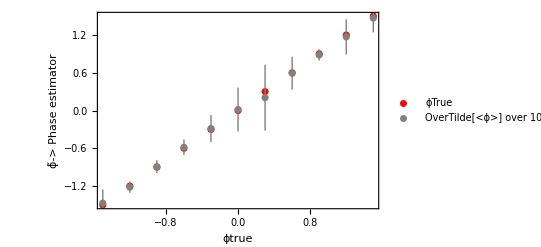

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevRMSE}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 100 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

```mathematica
(*Median +- MAD*)
```

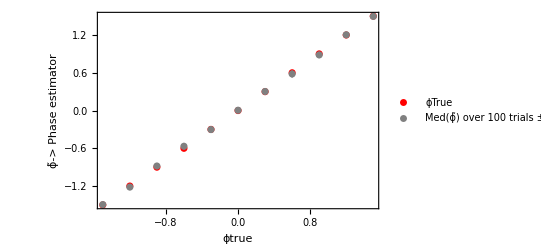

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevMAD}],PlotStyle->{Gray}, PlotLegends->{"Med(ϕ̃) over 100 trials ± MAD"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

## E. Probability of being unlucky - Check using MC

### Nph = 3

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.83 | π/10
-π/25 | -4/5 | 0.9 | π/10
-(3 π)/100 | -3/5 | 0.95 | π/10
-π/50 | -2/5 | 0.97 | π/10
-π/100 | -1/5 | 0.99 | π/10
0 | 0 | 1. | π/10
π/100 | 1/5 | 0.97 | π/10
π/50 | 2/5 | 0.99 | π/10
(3 π)/100 | 3/5 | 0.95 | π/10
π/25 | 4/5 | 0.91 | π/10
π/20 | 1 | 0.82 | π/10),(-π/10 | -1 | 0.9 | π/5
-(2 π)/25 | -4/5 | 0.9 | π/5
-(3 π)/50 | -3/5 | 0.93 | π/5
-π/25 | -2/5 | 0.99 | π/5
-π/50 | -1/5 | 0.95 | π/5
0 | 0 | 0.93 | π/5
π/50 | 1/5 | 0.97 | π/5
π/25 | 2/5 | 0.96 | π/5
(3 π)/50 | 3/5 | 0.92 | π/5
(2 π)/25 | 4/5 | 0.9 | π/5
π/10 | 1 | 0.9 | π/5),(-(3 π)/20 | -1 | 0.9 | (3 π)/10
-(3 π)/25 | -4/5 | 0.92 | (3 π)/10
-(9 π)/100 | -3/5 | 0.95 | (3 π)/10
-(3 π)/50 | -2/5 | 0.93 | (3 π)/10
-(3 π)/100 | -1/5 | 0.87 | (3 π)/10
0 | 0 | 0.92 | (3 π)/10
(3 π)/100 | 1/5 | 0.91 | (3 π)/10
(3 π)/50 | 2/5 | 0.92 | (3 π)/10
(9 π)/100 | 3/5 | 0.96 | (3 π)/10
(3 π)/25 | 4/5 | 0.94 | (3 π)/10
(3 π)/20 | 1 | 0.83 | (3 π)/10),(-π/5 | -1 | 0.88 | (2 π)/5
-(4 π)/25 | -4/5 | 0.96 | (2 π)/5
-(3 π)/25 | -3/5 | 0.94 | (2 π)/5
-(2 π)/25 | -2/5 | 0.9 | (2 π)/5
-π/25 | -1/5 | 0.9 | (2 π)/5
0 | 0 | 0.97 | (2 π)/5
π/25 | 1/5 | 0.91 | (2 π)/5
(2 π)/25 | 2/5 | 0.96 | (2 π)/5
(3 π)/25 | 3/5 | 0.94 | (2 π)/5
(4 π)/25 | 4/5 | 0.94 | (2 π)/5
π/5 | 1 | 0.75 | (2 π)/5),(-π/4 | -1 | 0.67 | π/2
-π/5 | -4/5 | 0.93 | π/2
-(3 π)/20 | -3/5 | 0.94 | π/2
-π/10 | -2/5 | 0.89 | π/2
-π/20 | -1/5 | 0.93 | π/2
0 | 0 | 0.89 | π/2
π/20 | 1/5 | 0.89 | π/2
π/10 | 2/5 | 0.97 | π/2
(3 π)/20 | 3/5 | 0.92 | π/2
π/5 | 4/5 | 0.95 | π/2
π/4 | 1 | 0.76 | π/2),(-π/2 | -1 | 0.92 | π
-(2 π)/5 | -4/5 | 0.84 | π
-(3 π)/10 | -3/5 | 0.92 | π
-π/5 | -2/5 | 0.89 | π
-π/10 | -1/5 | 0.9 | π
0 | 0 | 0.87 | π
π/10 | 1/5 | 0.92 | π
π/5 | 2/5 | 0.93 | π
(3 π)/10 | 3/5 | 0.85 | π
(2 π)/5 | 4/5 | 0.84 | π
π/2 | 1 | 0.93 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.83 | 0.9 | 0.95 | 0.97 | 0.99 | 1. | 0.97 | 0.99 | 0.95 | 0.91 | 0.82
0.9 | 0.9 | 0.93 | 0.99 | 0.95 | 0.93 | 0.97 | 0.96 | 0.92 | 0.9 | 0.9
0.9 | 0.92 | 0.95 | 0.93 | 0.87 | 0.92 | 0.91 | 0.92 | 0.96 | 0.94 | 0.83
0.88 | 0.96 | 0.94 | 0.9 | 0.9 | 0.97 | 0.91 | 0.96 | 0.94 | 0.94 | 0.75
0.67 | 0.93 | 0.94 | 0.89 | 0.93 | 0.89 | 0.89 | 0.97 | 0.92 | 0.95 | 0.76
0.92 | 0.84 | 0.92 | 0.89 | 0.9 | 0.87 | 0.92 | 0.93 | 0.85 | 0.84 | 0.93)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.830.04 | 0.9000.030 | 0.9500.022 | 0.9700.017 | 0.9900.010 | 1. | 0.9700.017 | 0.9900.010 | 0.9500.022 | 0.9100.029 | 0.820.04
0.9000.030 | 0.9000.030 | 0.9300.026 | 0.9900.010 | 0.9500.022 | 0.9300.026 | 0.9700.017 | 0.9600.020 | 0.9200.027 | 0.9000.030 | 0.9000.030
0.9000.030 | 0.9200.027 | 0.9500.022 | 0.9300.026 | 0.8700.034 | 0.9200.027 | 0.9100.029 | 0.9200.027 | 0.9600.020 | 0.9400.024 | 0.830.04
0.8800.032 | 0.9600.020 | 0.9400.024 | 0.9000.030 | 0.9000.030 | 0.9700.017 | 0.9100.029 | 0.9600.020 | 0.9400.024 | 0.9400.024 | 0.750.04
0.670.05 | 0.9300.026 | 0.9400.024 | 0.8900.031 | 0.9300.026 | 0.8900.031 | 0.8900.031 | 0.9700.017 | 0.9200.027 | 0.9500.022 | 0.760.04
0.9200.027 | 0.840.04 | 0.9200.027 | 0.8900.031 | 0.9000.030 | 0.8700.034 | 0.9200.027 | 0.9300.026 | 0.850.04 | 0.840.04 | 0.9300.026)

```mathematica
Average3=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.9350.007,0.9320.008,0.9140.008,0.9140.008,0.8850.009,0.8920.009}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.83) | (-4/5
0.9) | (-3/5
0.95) | (-2/5
0.97) | (-1/5
0.99) | (0
1.) | (1/5
0.97) | (2/5
0.99) | (3/5
0.95) | (4/5
0.91) | (1
0.82)
(-1
0.9) | (-4/5
0.9) | (-3/5
0.93) | (-2/5
0.99) | (-1/5
0.95) | (0
0.93) | (1/5
0.97) | (2/5
0.96) | (3/5
0.92) | (4/5
0.9) | (1
0.9)
(-1
0.9) | (-4/5
0.92) | (-3/5
0.95) | (-2/5
0.93) | (-1/5
0.87) | (0
0.92) | (1/5
0.91) | (2/5
0.92) | (3/5
0.96) | (4/5
0.94) | (1
0.83)
(-1
0.88) | (-4/5
0.96) | (-3/5
0.94) | (-2/5
0.9) | (-1/5
0.9) | (0
0.97) | (1/5
0.91) | (2/5
0.96) | (3/5
0.94) | (4/5
0.94) | (1
0.75)
(-1
0.67) | (-4/5
0.93) | (-3/5
0.94) | (-2/5
0.89) | (-1/5
0.93) | (0
0.89) | (1/5
0.89) | (2/5
0.97) | (3/5
0.92) | (4/5
0.95) | (1
0.76)
(-1
0.92) | (-4/5
0.84) | (-3/5
0.92) | (-2/5
0.89) | (-1/5
0.9) | (0
0.87) | (1/5
0.92) | (2/5
0.93) | (3/5
0.85) | (4/5
0.84) | (1
0.93))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.830.04) | (-4/5
0.9000.030) | (-3/5
0.9500.022) | (-2/5
0.9700.017) | (-1/5
0.9900.010) | (0
1.) | (1/5
0.9700.017) | (2/5
0.9900.010) | (3/5
0.9500.022) | (4/5
0.9100.029) | (1
0.820.04)
(-1
0.9000.030) | (-4/5
0.9000.030) | (-3/5
0.9300.026) | (-2/5
0.9900.010) | (-1/5
0.9500.022) | (0
0.9300.026) | (1/5
0.9700.017) | (2/5
0.9600.020) | (3/5
0.9200.027) | (4/5
0.9000.030) | (1
0.9000.030)
(-1
0.9000.030) | (-4/5
0.9200.027) | (-3/5
0.9500.022) | (-2/5
0.9300.026) | (-1/5
0.8700.034) | (0
0.9200.027) | (1/5
0.9100.029) | (2/5
0.9200.027) | (3/5
0.9600.020) | (4/5
0.9400.024) | (1
0.830.04)
(-1
0.8800.032) | (-4/5
0.9600.020) | (-3/5
0.9400.024) | (-2/5
0.9000.030) | (-1/5
0.9000.030) | (0
0.9700.017) | (1/5
0.9100.029) | (2/5
0.9600.020) | (3/5
0.9400.024) | (4/5
0.9400.024) | (1
0.750.04)
(-1
0.670.05) | (-4/5
0.9300.026) | (-3/5
0.9400.024) | (-2/5
0.8900.031) | (-1/5
0.9300.026) | (0
0.8900.031) | (1/5
0.8900.031) | (2/5
0.9700.017) | (3/5
0.9200.027) | (4/5
0.9500.022) | (1
0.760.04)
(-1
0.9200.027) | (-4/5
0.840.04) | (-3/5
0.9200.027) | (-2/5
0.8900.031) | (-1/5
0.9000.030) | (0
0.8700.034) | (1/5
0.9200.027) | (2/5
0.9300.026) | (3/5
0.850.04) | (4/5
0.840.04) | (1
0.9300.026))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

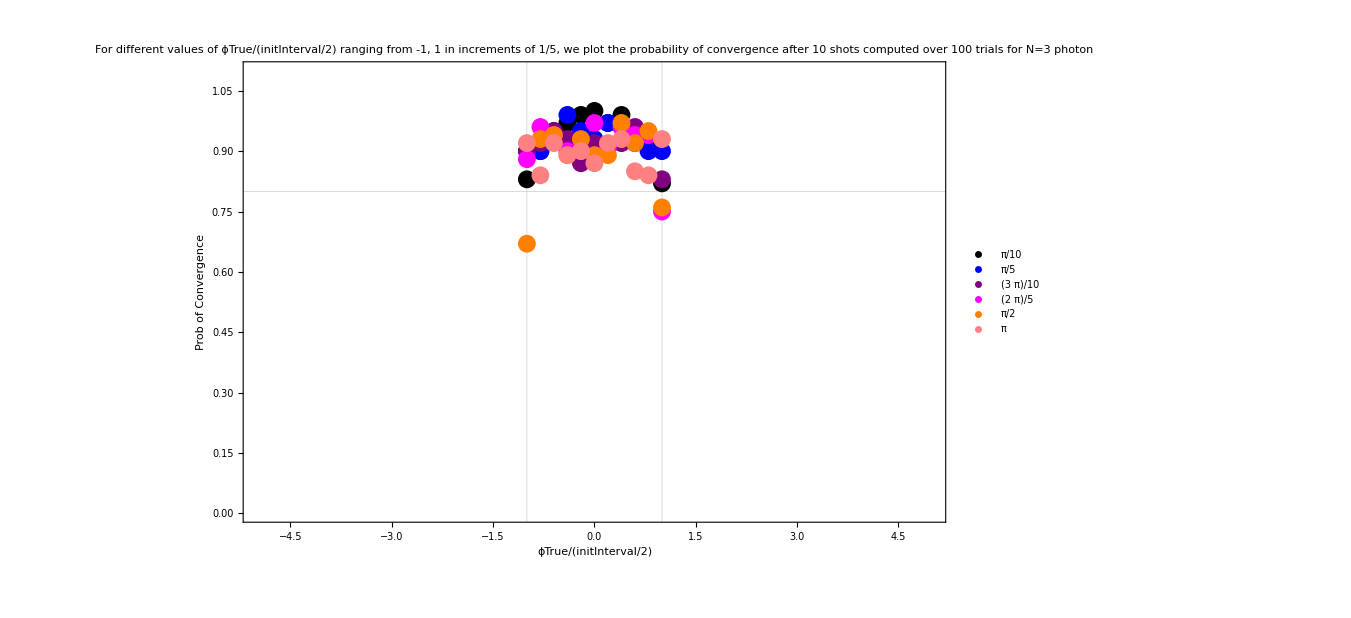

```mathematica
plot31=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

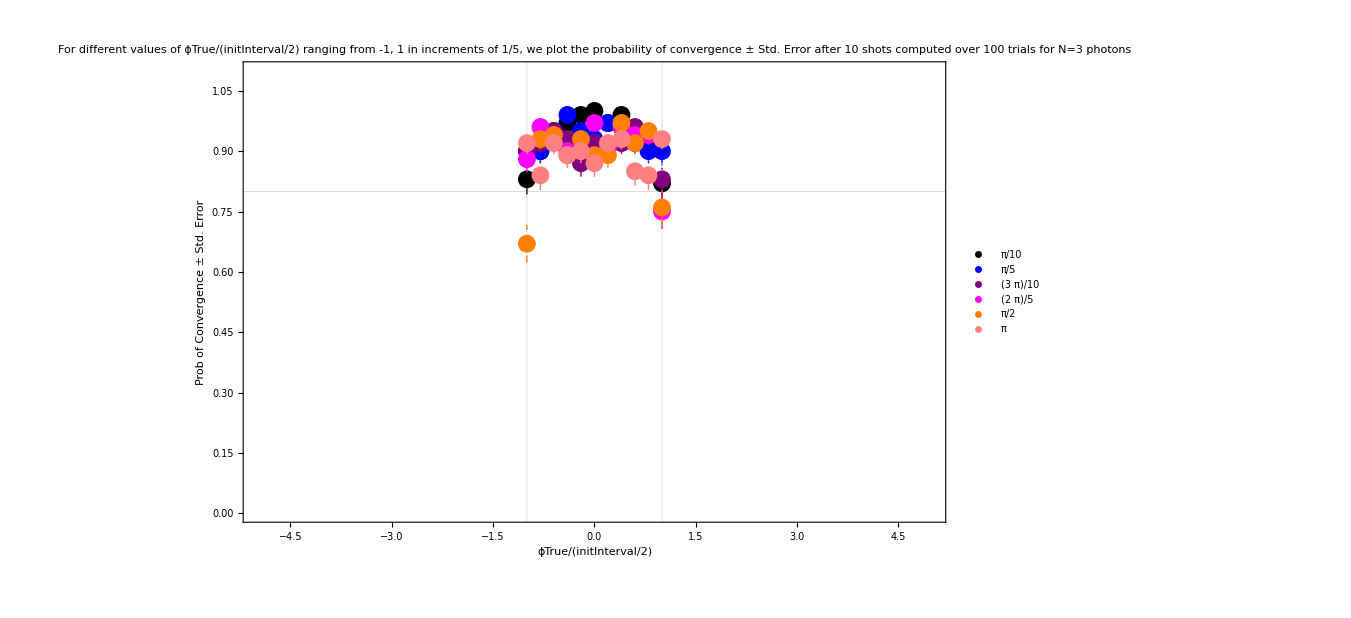

```mathematica
plot32=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=3 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

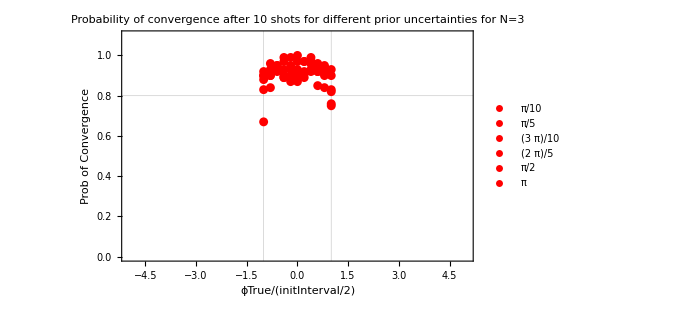

```mathematica
plot33=Show[ListPlot[plot[[1,1]],PlotStyle->{Red, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=3",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Red,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Red, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Red,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Red,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

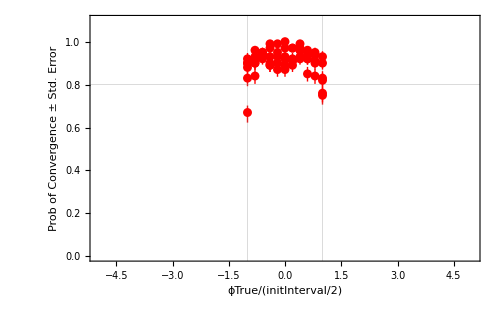

```mathematica
plot34=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Red, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Red, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Red,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
plot34=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average3
```

{0.9350.007,0.9320.008,0.9140.008,0.9140.008,0.8850.009,0.8920.009}

```mathematica
Around[Mean[Table[Average3[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average3[[n,1,2]],{n,1,Length[Data]}]]]
```

0.9120.008

```mathematica
Average3=0.9120.008
```

0.9120.008

```mathematica
Average3=Around[Average3[[1]],Sqrt[Average3[[1]](1-Average3[[1]])/100]]
```

0.9120.028

### Nph = 5

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=5;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.85 | π/10
-π/25 | -4/5 | 0.89 | π/10
-(3 π)/100 | -3/5 | 0.92 | π/10
-π/50 | -2/5 | 0.96 | π/10
-π/100 | -1/5 | 0.95 | π/10
0 | 0 | 0.98 | π/10
π/100 | 1/5 | 0.97 | π/10
π/50 | 2/5 | 0.9 | π/10
(3 π)/100 | 3/5 | 0.92 | π/10
π/25 | 4/5 | 0.88 | π/10
π/20 | 1 | 0.79 | π/10),(-π/10 | -1 | 0.77 | π/5
-(2 π)/25 | -4/5 | 0.9 | π/5
-(3 π)/50 | -3/5 | 0.87 | π/5
-π/25 | -2/5 | 0.95 | π/5
-π/50 | -1/5 | 0.95 | π/5
0 | 0 | 0.89 | π/5
π/50 | 1/5 | 0.92 | π/5
π/25 | 2/5 | 0.92 | π/5
(3 π)/50 | 3/5 | 0.86 | π/5
(2 π)/25 | 4/5 | 0.93 | π/5
π/10 | 1 | 0.78 | π/5),(-(3 π)/20 | -1 | 0.78 | (3 π)/10
-(3 π)/25 | -4/5 | 0.94 | (3 π)/10
-(9 π)/100 | -3/5 | 0.96 | (3 π)/10
-(3 π)/50 | -2/5 | 0.94 | (3 π)/10
-(3 π)/100 | -1/5 | 0.91 | (3 π)/10
0 | 0 | 0.9 | (3 π)/10
(3 π)/100 | 1/5 | 0.92 | (3 π)/10
(3 π)/50 | 2/5 | 0.93 | (3 π)/10
(9 π)/100 | 3/5 | 0.93 | (3 π)/10
(3 π)/25 | 4/5 | 0.92 | (3 π)/10
(3 π)/20 | 1 | 0.8 | (3 π)/10),(-π/5 | -1 | 0.91 | (2 π)/5
-(4 π)/25 | -4/5 | 0.93 | (2 π)/5
-(3 π)/25 | -3/5 | 0.89 | (2 π)/5
-(2 π)/25 | -2/5 | 0.91 | (2 π)/5
-π/25 | -1/5 | 0.88 | (2 π)/5
0 | 0 | 0.92 | (2 π)/5
π/25 | 1/5 | 0.89 | (2 π)/5
(2 π)/25 | 2/5 | 0.93 | (2 π)/5
(3 π)/25 | 3/5 | 0.88 | (2 π)/5
(4 π)/25 | 4/5 | 0.88 | (2 π)/5
π/5 | 1 | 0.91 | (2 π)/5),(-π/4 | -1 | 0.89 | π/2
-π/5 | -4/5 | 0.87 | π/2
-(3 π)/20 | -3/5 | 0.88 | π/2
-π/10 | -2/5 | 0.89 | π/2
-π/20 | -1/5 | 0.89 | π/2
0 | 0 | 0.85 | π/2
π/20 | 1/5 | 0.92 | π/2
π/10 | 2/5 | 0.91 | π/2
(3 π)/20 | 3/5 | 0.9 | π/2
π/5 | 4/5 | 0.9 | π/2
π/4 | 1 | 0.88 | π/2),(-π/2 | -1 | 0.84 | π
-(2 π)/5 | -4/5 | 0.91 | π
-(3 π)/10 | -3/5 | 0.93 | π
-π/5 | -2/5 | 0.91 | π
-π/10 | -1/5 | 0.9 | π
0 | 0 | 0.88 | π
π/10 | 1/5 | 0.9 | π
π/5 | 2/5 | 0.85 | π
(3 π)/10 | 3/5 | 0.92 | π
(2 π)/5 | 4/5 | 0.81 | π
π/2 | 1 | 0.85 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.85 | 0.89 | 0.92 | 0.96 | 0.95 | 0.98 | 0.97 | 0.9 | 0.92 | 0.88 | 0.79
0.77 | 0.9 | 0.87 | 0.95 | 0.95 | 0.89 | 0.92 | 0.92 | 0.86 | 0.93 | 0.78
0.78 | 0.94 | 0.96 | 0.94 | 0.91 | 0.9 | 0.92 | 0.93 | 0.93 | 0.92 | 0.8
0.91 | 0.93 | 0.89 | 0.91 | 0.88 | 0.92 | 0.89 | 0.93 | 0.88 | 0.88 | 0.91
0.89 | 0.87 | 0.88 | 0.89 | 0.89 | 0.85 | 0.92 | 0.91 | 0.9 | 0.9 | 0.88
0.84 | 0.91 | 0.93 | 0.91 | 0.9 | 0.88 | 0.9 | 0.85 | 0.92 | 0.81 | 0.85)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.850.04 | 0.8900.031 | 0.9200.027 | 0.9600.020 | 0.9500.022 | 0.9800.014 | 0.9700.017 | 0.9000.030 | 0.9200.027 | 0.8800.032 | 0.790.04
0.770.04 | 0.9000.030 | 0.8700.034 | 0.9500.022 | 0.9500.022 | 0.8900.031 | 0.9200.027 | 0.9200.027 | 0.8600.035 | 0.9300.026 | 0.780.04
0.780.04 | 0.9400.024 | 0.9600.020 | 0.9400.024 | 0.9100.029 | 0.9000.030 | 0.9200.027 | 0.9300.026 | 0.9300.026 | 0.9200.027 | 0.800.04
0.9100.029 | 0.9300.026 | 0.8900.031 | 0.9100.029 | 0.8800.032 | 0.9200.027 | 0.8900.031 | 0.9300.026 | 0.8800.032 | 0.8800.032 | 0.9100.029
0.8900.031 | 0.8700.034 | 0.8800.032 | 0.8900.031 | 0.8900.031 | 0.850.04 | 0.9200.027 | 0.9100.029 | 0.9000.030 | 0.9000.030 | 0.8800.032
0.840.04 | 0.9100.029 | 0.9300.026 | 0.9100.029 | 0.9000.030 | 0.8800.032 | 0.9000.030 | 0.850.04 | 0.9200.027 | 0.810.04 | 0.850.04)

```mathematica
Average3=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.9100.008,0.8850.009,0.9030.009,0.9030.009,0.8890.009,0.8820.010}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.85) | (-4/5
0.89) | (-3/5
0.92) | (-2/5
0.96) | (-1/5
0.95) | (0
0.98) | (1/5
0.97) | (2/5
0.9) | (3/5
0.92) | (4/5
0.88) | (1
0.79)
(-1
0.77) | (-4/5
0.9) | (-3/5
0.87) | (-2/5
0.95) | (-1/5
0.95) | (0
0.89) | (1/5
0.92) | (2/5
0.92) | (3/5
0.86) | (4/5
0.93) | (1
0.78)
(-1
0.78) | (-4/5
0.94) | (-3/5
0.96) | (-2/5
0.94) | (-1/5
0.91) | (0
0.9) | (1/5
0.92) | (2/5
0.93) | (3/5
0.93) | (4/5
0.92) | (1
0.8)
(-1
0.91) | (-4/5
0.93) | (-3/5
0.89) | (-2/5
0.91) | (-1/5
0.88) | (0
0.92) | (1/5
0.89) | (2/5
0.93) | (3/5
0.88) | (4/5
0.88) | (1
0.91)
(-1
0.89) | (-4/5
0.87) | (-3/5
0.88) | (-2/5
0.89) | (-1/5
0.89) | (0
0.85) | (1/5
0.92) | (2/5
0.91) | (3/5
0.9) | (4/5
0.9) | (1
0.88)
(-1
0.84) | (-4/5
0.91) | (-3/5
0.93) | (-2/5
0.91) | (-1/5
0.9) | (0
0.88) | (1/5
0.9) | (2/5
0.85) | (3/5
0.92) | (4/5
0.81) | (1
0.85))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.850.04) | (-4/5
0.8900.031) | (-3/5
0.9200.027) | (-2/5
0.9600.020) | (-1/5
0.9500.022) | (0
0.9800.014) | (1/5
0.9700.017) | (2/5
0.9000.030) | (3/5
0.9200.027) | (4/5
0.8800.032) | (1
0.790.04)
(-1
0.770.04) | (-4/5
0.9000.030) | (-3/5
0.8700.034) | (-2/5
0.9500.022) | (-1/5
0.9500.022) | (0
0.8900.031) | (1/5
0.9200.027) | (2/5
0.9200.027) | (3/5
0.8600.035) | (4/5
0.9300.026) | (1
0.780.04)
(-1
0.780.04) | (-4/5
0.9400.024) | (-3/5
0.9600.020) | (-2/5
0.9400.024) | (-1/5
0.9100.029) | (0
0.9000.030) | (1/5
0.9200.027) | (2/5
0.9300.026) | (3/5
0.9300.026) | (4/5
0.9200.027) | (1
0.800.04)
(-1
0.9100.029) | (-4/5
0.9300.026) | (-3/5
0.8900.031) | (-2/5
0.9100.029) | (-1/5
0.8800.032) | (0
0.9200.027) | (1/5
0.8900.031) | (2/5
0.9300.026) | (3/5
0.8800.032) | (4/5
0.8800.032) | (1
0.9100.029)
(-1
0.8900.031) | (-4/5
0.8700.034) | (-3/5
0.8800.032) | (-2/5
0.8900.031) | (-1/5
0.8900.031) | (0
0.850.04) | (1/5
0.9200.027) | (2/5
0.9100.029) | (3/5
0.9000.030) | (4/5
0.9000.030) | (1
0.8800.032)
(-1
0.840.04) | (-4/5
0.9100.029) | (-3/5
0.9300.026) | (-2/5
0.9100.029) | (-1/5
0.9000.030) | (0
0.8800.032) | (1/5
0.9000.030) | (2/5
0.850.04) | (3/5
0.9200.027) | (4/5
0.810.04) | (1
0.850.04))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

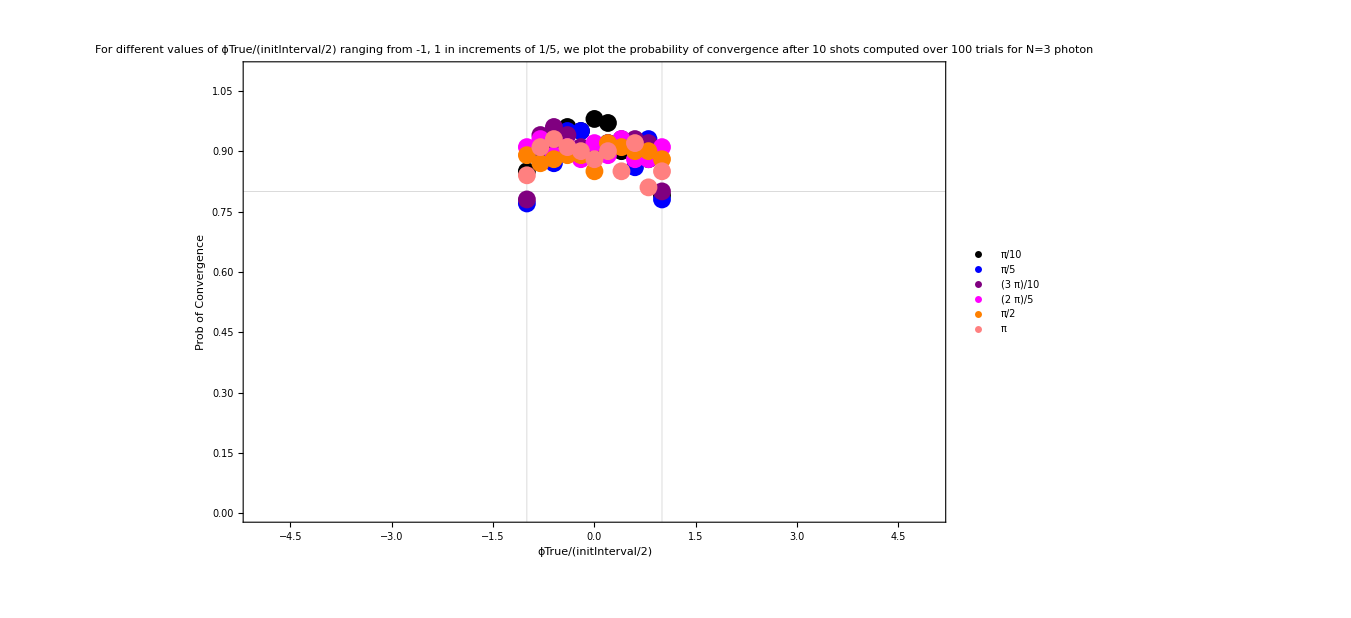

```mathematica
plot31=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

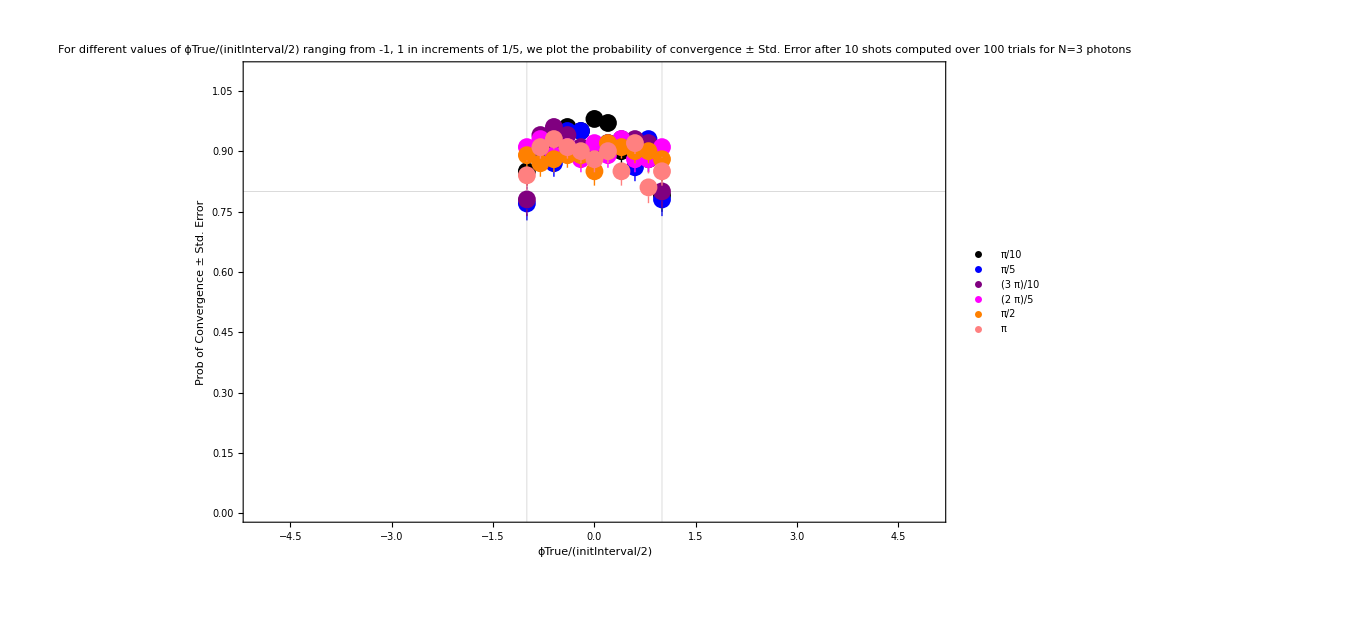

```mathematica
plot32=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=3 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

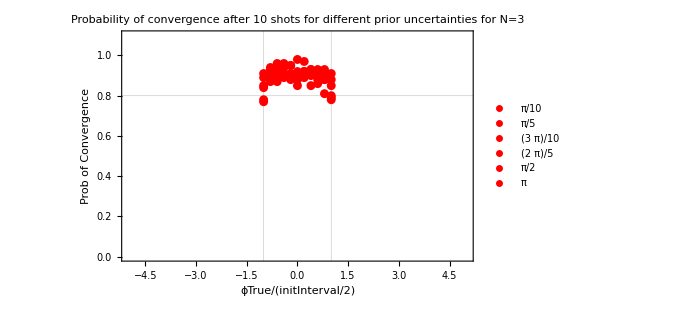

```mathematica
plot33=Show[ListPlot[plot[[1,1]],PlotStyle->{Red, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=3",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Red,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Red, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Red,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Red,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

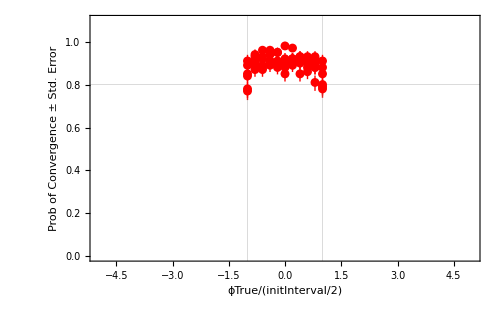

```mathematica
plot34=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Red, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Red, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Red,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
plot54=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average3
```

{0.9100.008,0.8850.009,0.9030.009,0.9030.009,0.8890.009,0.8820.010}

```mathematica
Average3=Around[Mean[Table[Average3[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average3[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8950.009

```mathematica
Average5=0.8950.009
```

0.8950.009

```mathematica
Average5=Around[Average5[[1]],Sqrt[Average5[[1]](1-Average5[[1]])/100]]
```

0.8950.031

### Nph = 7

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=7;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.86 | π/10
-π/25 | -4/5 | 0.88 | π/10
-(3 π)/100 | -3/5 | 0.91 | π/10
-π/50 | -2/5 | 0.94 | π/10
-π/100 | -1/5 | 0.94 | π/10
0 | 0 | 0.93 | π/10
π/100 | 1/5 | 0.94 | π/10
π/50 | 2/5 | 0.94 | π/10
(3 π)/100 | 3/5 | 0.92 | π/10
π/25 | 4/5 | 0.88 | π/10
π/20 | 1 | 0.89 | π/10),(-π/10 | -1 | 0.85 | π/5
-(2 π)/25 | -4/5 | 0.93 | π/5
-(3 π)/50 | -3/5 | 0.97 | π/5
-π/25 | -2/5 | 0.89 | π/5
-π/50 | -1/5 | 0.91 | π/5
0 | 0 | 0.83 | π/5
π/50 | 1/5 | 0.93 | π/5
π/25 | 2/5 | 0.87 | π/5
(3 π)/50 | 3/5 | 0.93 | π/5
(2 π)/25 | 4/5 | 0.93 | π/5
π/10 | 1 | 0.81 | π/5),(-(3 π)/20 | -1 | 0.92 | (3 π)/10
-(3 π)/25 | -4/5 | 0.92 | (3 π)/10
-(9 π)/100 | -3/5 | 0.87 | (3 π)/10
-(3 π)/50 | -2/5 | 0.9 | (3 π)/10
-(3 π)/100 | -1/5 | 0.89 | (3 π)/10
0 | 0 | 0.94 | (3 π)/10
(3 π)/100 | 1/5 | 0.89 | (3 π)/10
(3 π)/50 | 2/5 | 0.91 | (3 π)/10
(9 π)/100 | 3/5 | 0.83 | (3 π)/10
(3 π)/25 | 4/5 | 0.87 | (3 π)/10
(3 π)/20 | 1 | 0.94 | (3 π)/10),(-π/5 | -1 | 0.9 | (2 π)/5
-(4 π)/25 | -4/5 | 0.92 | (2 π)/5
-(3 π)/25 | -3/5 | 0.84 | (2 π)/5
-(2 π)/25 | -2/5 | 0.94 | (2 π)/5
-π/25 | -1/5 | 0.93 | (2 π)/5
0 | 0 | 0.87 | (2 π)/5
π/25 | 1/5 | 0.88 | (2 π)/5
(2 π)/25 | 2/5 | 0.91 | (2 π)/5
(3 π)/25 | 3/5 | 0.89 | (2 π)/5
(4 π)/25 | 4/5 | 0.89 | (2 π)/5
π/5 | 1 | 0.94 | (2 π)/5),(-π/4 | -1 | 0.84 | π/2
-π/5 | -4/5 | 0.95 | π/2
-(3 π)/20 | -3/5 | 0.94 | π/2
-π/10 | -2/5 | 0.96 | π/2
-π/20 | -1/5 | 0.94 | π/2
0 | 0 | 0.83 | π/2
π/20 | 1/5 | 0.92 | π/2
π/10 | 2/5 | 0.91 | π/2
(3 π)/20 | 3/5 | 0.94 | π/2
π/5 | 4/5 | 0.97 | π/2
π/4 | 1 | 0.82 | π/2),(-π/2 | -1 | 0.89 | π
-(2 π)/5 | -4/5 | 0.92 | π
-(3 π)/10 | -3/5 | 0.89 | π
-π/5 | -2/5 | 0.85 | π
-π/10 | -1/5 | 0.84 | π
0 | 0 | 0.78 | π
π/10 | 1/5 | 0.86 | π
π/5 | 2/5 | 0.77 | π
(3 π)/10 | 3/5 | 0.86 | π
(2 π)/5 | 4/5 | 0.92 | π
π/2 | 1 | 0.87 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.86 | 0.88 | 0.91 | 0.94 | 0.94 | 0.93 | 0.94 | 0.94 | 0.92 | 0.88 | 0.89
0.85 | 0.93 | 0.97 | 0.89 | 0.91 | 0.83 | 0.93 | 0.87 | 0.93 | 0.93 | 0.81
0.92 | 0.92 | 0.87 | 0.9 | 0.89 | 0.94 | 0.89 | 0.91 | 0.83 | 0.87 | 0.94
0.9 | 0.92 | 0.84 | 0.94 | 0.93 | 0.87 | 0.88 | 0.91 | 0.89 | 0.89 | 0.94
0.84 | 0.95 | 0.94 | 0.96 | 0.94 | 0.83 | 0.92 | 0.91 | 0.94 | 0.97 | 0.82
0.89 | 0.92 | 0.89 | 0.85 | 0.84 | 0.78 | 0.86 | 0.77 | 0.86 | 0.92 | 0.87)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.8600.035 | 0.8800.032 | 0.9100.029 | 0.9400.024 | 0.9400.024 | 0.9300.026 | 0.9400.024 | 0.9400.024 | 0.9200.027 | 0.8800.032 | 0.8900.031
0.850.04 | 0.9300.026 | 0.9700.017 | 0.8900.031 | 0.9100.029 | 0.830.04 | 0.9300.026 | 0.8700.034 | 0.9300.026 | 0.9300.026 | 0.810.04
0.9200.027 | 0.9200.027 | 0.8700.034 | 0.9000.030 | 0.8900.031 | 0.9400.024 | 0.8900.031 | 0.9100.029 | 0.830.04 | 0.8700.034 | 0.9400.024
0.9000.030 | 0.9200.027 | 0.840.04 | 0.9400.024 | 0.9300.026 | 0.8700.034 | 0.8800.032 | 0.9100.029 | 0.8900.031 | 0.8900.031 | 0.9400.024
0.840.04 | 0.9500.022 | 0.9400.024 | 0.9600.020 | 0.9400.024 | 0.830.04 | 0.9200.027 | 0.9100.029 | 0.9400.024 | 0.9700.017 | 0.820.04
0.8900.031 | 0.9200.027 | 0.8900.031 | 0.850.04 | 0.840.04 | 0.780.04 | 0.8600.035 | 0.770.04 | 0.8600.035 | 0.9200.027 | 0.8700.034)

```mathematica
Average7=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.9120.009,0.8950.009,0.8980.009,0.9010.009,0.9110.008,0.8590.010}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.86) | (-4/5
0.88) | (-3/5
0.91) | (-2/5
0.94) | (-1/5
0.94) | (0
0.93) | (1/5
0.94) | (2/5
0.94) | (3/5
0.92) | (4/5
0.88) | (1
0.89)
(-1
0.85) | (-4/5
0.93) | (-3/5
0.97) | (-2/5
0.89) | (-1/5
0.91) | (0
0.83) | (1/5
0.93) | (2/5
0.87) | (3/5
0.93) | (4/5
0.93) | (1
0.81)
(-1
0.92) | (-4/5
0.92) | (-3/5
0.87) | (-2/5
0.9) | (-1/5
0.89) | (0
0.94) | (1/5
0.89) | (2/5
0.91) | (3/5
0.83) | (4/5
0.87) | (1
0.94)
(-1
0.9) | (-4/5
0.92) | (-3/5
0.84) | (-2/5
0.94) | (-1/5
0.93) | (0
0.87) | (1/5
0.88) | (2/5
0.91) | (3/5
0.89) | (4/5
0.89) | (1
0.94)
(-1
0.84) | (-4/5
0.95) | (-3/5
0.94) | (-2/5
0.96) | (-1/5
0.94) | (0
0.83) | (1/5
0.92) | (2/5
0.91) | (3/5
0.94) | (4/5
0.97) | (1
0.82)
(-1
0.89) | (-4/5
0.92) | (-3/5
0.89) | (-2/5
0.85) | (-1/5
0.84) | (0
0.78) | (1/5
0.86) | (2/5
0.77) | (3/5
0.86) | (4/5
0.92) | (1
0.87))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.8600.035) | (-4/5
0.8800.032) | (-3/5
0.9100.029) | (-2/5
0.9400.024) | (-1/5
0.9400.024) | (0
0.9300.026) | (1/5
0.9400.024) | (2/5
0.9400.024) | (3/5
0.9200.027) | (4/5
0.8800.032) | (1
0.8900.031)
(-1
0.850.04) | (-4/5
0.9300.026) | (-3/5
0.9700.017) | (-2/5
0.8900.031) | (-1/5
0.9100.029) | (0
0.830.04) | (1/5
0.9300.026) | (2/5
0.8700.034) | (3/5
0.9300.026) | (4/5
0.9300.026) | (1
0.810.04)
(-1
0.9200.027) | (-4/5
0.9200.027) | (-3/5
0.8700.034) | (-2/5
0.9000.030) | (-1/5
0.8900.031) | (0
0.9400.024) | (1/5
0.8900.031) | (2/5
0.9100.029) | (3/5
0.830.04) | (4/5
0.8700.034) | (1
0.9400.024)
(-1
0.9000.030) | (-4/5
0.9200.027) | (-3/5
0.840.04) | (-2/5
0.9400.024) | (-1/5
0.9300.026) | (0
0.8700.034) | (1/5
0.8800.032) | (2/5
0.9100.029) | (3/5
0.8900.031) | (4/5
0.8900.031) | (1
0.9400.024)
(-1
0.840.04) | (-4/5
0.9500.022) | (-3/5
0.9400.024) | (-2/5
0.9600.020) | (-1/5
0.9400.024) | (0
0.830.04) | (1/5
0.9200.027) | (2/5
0.9100.029) | (3/5
0.9400.024) | (4/5
0.9700.017) | (1
0.820.04)
(-1
0.8900.031) | (-4/5
0.9200.027) | (-3/5
0.8900.031) | (-2/5
0.850.04) | (-1/5
0.840.04) | (0
0.780.04) | (1/5
0.8600.035) | (2/5
0.770.04) | (3/5
0.8600.035) | (4/5
0.9200.027) | (1
0.8700.034))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

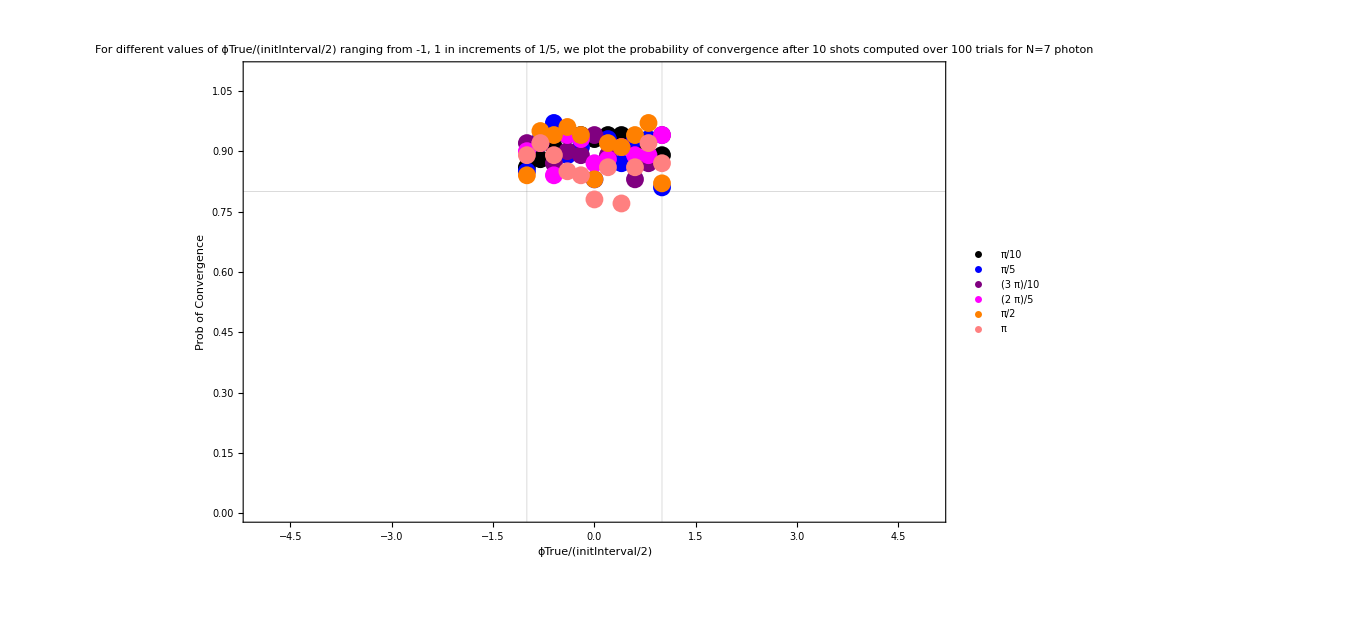

```mathematica
plot71=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=7 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

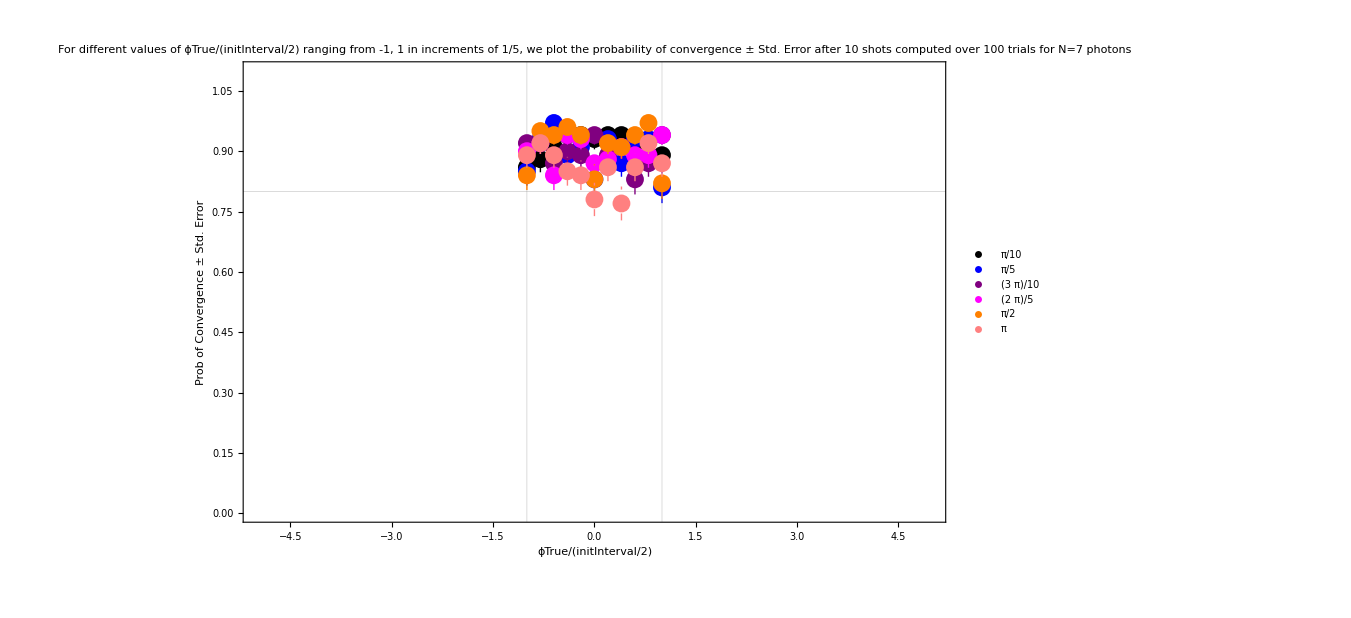

```mathematica
plot72=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=7 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

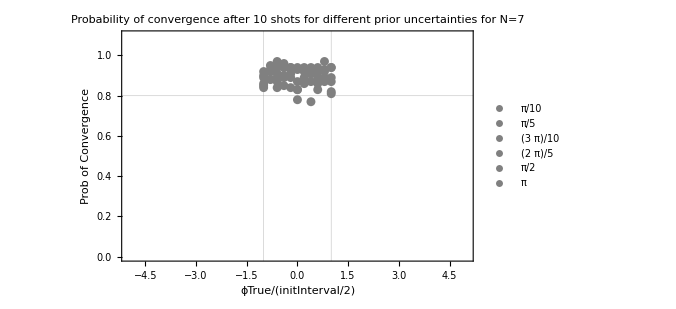

```mathematica
plot73=Show[ListPlot[plot[[1,1]],PlotStyle->{Gray, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=7",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Gray,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Gray, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Gray,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Gray,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Gray,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

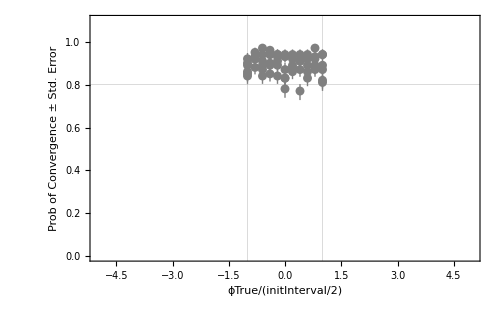

```mathematica
plot74=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Gray, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Gray, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Gray,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

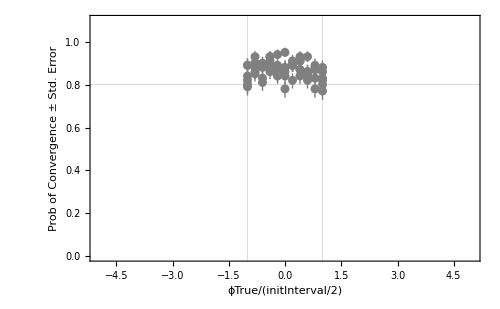
```mathematica
plot74=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average7
```

{0.9120.009,0.8950.009,0.8980.009,0.9010.009,0.9110.008,0.8590.010}

```mathematica
Average7=Around[Mean[Table[Average7[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average7[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8960.009

```mathematica
Average7=0.8960.009
```

0.8960.009

```mathematica
Average7=Around[Average7[[1]],Sqrt[Average7[[1]](1-Average7[[1]])/100]]
```

0.8960.031

### Nph = 10

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.71 | π/10
-π/25 | -4/5 | 0.9 | π/10
-(3 π)/100 | -3/5 | 0.82 | π/10
-π/50 | -2/5 | 0.87 | π/10
-π/100 | -1/5 | 0.91 | π/10
0 | 0 | 0.9 | π/10
π/100 | 1/5 | 0.93 | π/10
π/50 | 2/5 | 0.9 | π/10
(3 π)/100 | 3/5 | 0.94 | π/10
π/25 | 4/5 | 0.91 | π/10
π/20 | 1 | 0.81 | π/10),(-π/10 | -1 | 0.83 | π/5
-(2 π)/25 | -4/5 | 0.9 | π/5
-(3 π)/50 | -3/5 | 0.9 | π/5
-π/25 | -2/5 | 0.93 | π/5
-π/50 | -1/5 | 0.85 | π/5
0 | 0 | 0.86 | π/5
π/50 | 1/5 | 0.89 | π/5
π/25 | 2/5 | 0.94 | π/5
(3 π)/50 | 3/5 | 0.93 | π/5
(2 π)/25 | 4/5 | 0.89 | π/5
π/10 | 1 | 0.79 | π/5),(-(3 π)/20 | -1 | 0.95 | (3 π)/10
-(3 π)/25 | -4/5 | 0.91 | (3 π)/10
-(9 π)/100 | -3/5 | 0.81 | (3 π)/10
-(3 π)/50 | -2/5 | 0.84 | (3 π)/10
-(3 π)/100 | -1/5 | 0.88 | (3 π)/10
0 | 0 | 0.9 | (3 π)/10
(3 π)/100 | 1/5 | 0.93 | (3 π)/10
(3 π)/50 | 2/5 | 0.9 | (3 π)/10
(9 π)/100 | 3/5 | 0.91 | (3 π)/10
(3 π)/25 | 4/5 | 0.93 | (3 π)/10
(3 π)/20 | 1 | 0.85 | (3 π)/10),(-π/5 | -1 | 0.91 | (2 π)/5
-(4 π)/25 | -4/5 | 0.94 | (2 π)/5
-(3 π)/25 | -3/5 | 0.92 | (2 π)/5
-(2 π)/25 | -2/5 | 0.77 | (2 π)/5
-π/25 | -1/5 | 0.87 | (2 π)/5
0 | 0 | 0.77 | (2 π)/5
π/25 | 1/5 | 0.89 | (2 π)/5
(2 π)/25 | 2/5 | 0.87 | (2 π)/5
(3 π)/25 | 3/5 | 0.92 | (2 π)/5
(4 π)/25 | 4/5 | 0.96 | (2 π)/5
π/5 | 1 | 0.86 | (2 π)/5),(-π/4 | -1 | 0.94 | π/2
-π/5 | -4/5 | 0.88 | π/2
-(3 π)/20 | -3/5 | 0.93 | π/2
-π/10 | -2/5 | 0.86 | π/2
-π/20 | -1/5 | 0.89 | π/2
0 | 0 | 0.87 | π/2
π/20 | 1/5 | 0.97 | π/2
π/10 | 2/5 | 0.85 | π/2
(3 π)/20 | 3/5 | 0.91 | π/2
π/5 | 4/5 | 0.89 | π/2
π/4 | 1 | 0.92 | π/2),(-π/2 | -1 | 0.87 | π
-(2 π)/5 | -4/5 | 0.9 | π
-(3 π)/10 | -3/5 | 0.88 | π
-π/5 | -2/5 | 0.86 | π
-π/10 | -1/5 | 0.81 | π
0 | 0 | 0.84 | π
π/10 | 1/5 | 0.81 | π
π/5 | 2/5 | 0.83 | π
(3 π)/10 | 3/5 | 0.89 | π
(2 π)/5 | 4/5 | 0.89 | π
π/2 | 1 | 0.9 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.71 | 0.9 | 0.82 | 0.87 | 0.91 | 0.9 | 0.93 | 0.9 | 0.94 | 0.91 | 0.81
0.83 | 0.9 | 0.9 | 0.93 | 0.85 | 0.86 | 0.89 | 0.94 | 0.93 | 0.89 | 0.79
0.95 | 0.91 | 0.81 | 0.84 | 0.88 | 0.9 | 0.93 | 0.9 | 0.91 | 0.93 | 0.85
0.91 | 0.94 | 0.92 | 0.77 | 0.87 | 0.77 | 0.89 | 0.87 | 0.92 | 0.96 | 0.86
0.94 | 0.88 | 0.93 | 0.86 | 0.89 | 0.87 | 0.97 | 0.85 | 0.91 | 0.89 | 0.92
0.87 | 0.9 | 0.88 | 0.86 | 0.81 | 0.84 | 0.81 | 0.83 | 0.89 | 0.89 | 0.9)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.710.05 | 0.9000.030 | 0.820.04 | 0.8700.034 | 0.9100.029 | 0.9000.030 | 0.9300.026 | 0.9000.030 | 0.9400.024 | 0.9100.029 | 0.810.04
0.830.04 | 0.9000.030 | 0.9000.030 | 0.9300.026 | 0.850.04 | 0.8600.035 | 0.8900.031 | 0.9400.024 | 0.9300.026 | 0.8900.031 | 0.790.04
0.9500.022 | 0.9100.029 | 0.810.04 | 0.840.04 | 0.8800.032 | 0.9000.030 | 0.9300.026 | 0.9000.030 | 0.9100.029 | 0.9300.026 | 0.850.04
0.9100.029 | 0.9400.024 | 0.9200.027 | 0.770.04 | 0.8700.034 | 0.770.04 | 0.8900.031 | 0.8700.034 | 0.9200.027 | 0.9600.020 | 0.8600.035
0.9400.024 | 0.8800.032 | 0.9300.026 | 0.8600.035 | 0.8900.031 | 0.8700.034 | 0.9700.017 | 0.850.04 | 0.9100.029 | 0.8900.031 | 0.9200.027
0.8700.034 | 0.9000.030 | 0.8800.032 | 0.8600.035 | 0.810.04 | 0.840.04 | 0.810.04 | 0.830.04 | 0.8900.031 | 0.8900.031 | 0.9000.030)

```mathematica
Average10=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.8730.010,0.8830.010,0.8920.009,0.8800.010,0.9010.009,0.8620.010}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.71) | (-4/5
0.9) | (-3/5
0.82) | (-2/5
0.87) | (-1/5
0.91) | (0
0.9) | (1/5
0.93) | (2/5
0.9) | (3/5
0.94) | (4/5
0.91) | (1
0.81)
(-1
0.83) | (-4/5
0.9) | (-3/5
0.9) | (-2/5
0.93) | (-1/5
0.85) | (0
0.86) | (1/5
0.89) | (2/5
0.94) | (3/5
0.93) | (4/5
0.89) | (1
0.79)
(-1
0.95) | (-4/5
0.91) | (-3/5
0.81) | (-2/5
0.84) | (-1/5
0.88) | (0
0.9) | (1/5
0.93) | (2/5
0.9) | (3/5
0.91) | (4/5
0.93) | (1
0.85)
(-1
0.91) | (-4/5
0.94) | (-3/5
0.92) | (-2/5
0.77) | (-1/5
0.87) | (0
0.77) | (1/5
0.89) | (2/5
0.87) | (3/5
0.92) | (4/5
0.96) | (1
0.86)
(-1
0.94) | (-4/5
0.88) | (-3/5
0.93) | (-2/5
0.86) | (-1/5
0.89) | (0
0.87) | (1/5
0.97) | (2/5
0.85) | (3/5
0.91) | (4/5
0.89) | (1
0.92)
(-1
0.87) | (-4/5
0.9) | (-3/5
0.88) | (-2/5
0.86) | (-1/5
0.81) | (0
0.84) | (1/5
0.81) | (2/5
0.83) | (3/5
0.89) | (4/5
0.89) | (1
0.9))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.710.05) | (-4/5
0.9000.030) | (-3/5
0.820.04) | (-2/5
0.8700.034) | (-1/5
0.9100.029) | (0
0.9000.030) | (1/5
0.9300.026) | (2/5
0.9000.030) | (3/5
0.9400.024) | (4/5
0.9100.029) | (1
0.810.04)
(-1
0.830.04) | (-4/5
0.9000.030) | (-3/5
0.9000.030) | (-2/5
0.9300.026) | (-1/5
0.850.04) | (0
0.8600.035) | (1/5
0.8900.031) | (2/5
0.9400.024) | (3/5
0.9300.026) | (4/5
0.8900.031) | (1
0.790.04)
(-1
0.9500.022) | (-4/5
0.9100.029) | (-3/5
0.810.04) | (-2/5
0.840.04) | (-1/5
0.8800.032) | (0
0.9000.030) | (1/5
0.9300.026) | (2/5
0.9000.030) | (3/5
0.9100.029) | (4/5
0.9300.026) | (1
0.850.04)
(-1
0.9100.029) | (-4/5
0.9400.024) | (-3/5
0.9200.027) | (-2/5
0.770.04) | (-1/5
0.8700.034) | (0
0.770.04) | (1/5
0.8900.031) | (2/5
0.8700.034) | (3/5
0.9200.027) | (4/5
0.9600.020) | (1
0.8600.035)
(-1
0.9400.024) | (-4/5
0.8800.032) | (-3/5
0.9300.026) | (-2/5
0.8600.035) | (-1/5
0.8900.031) | (0
0.8700.034) | (1/5
0.9700.017) | (2/5
0.850.04) | (3/5
0.9100.029) | (4/5
0.8900.031) | (1
0.9200.027)
(-1
0.8700.034) | (-4/5
0.9000.030) | (-3/5
0.8800.032) | (-2/5
0.8600.035) | (-1/5
0.810.04) | (0
0.840.04) | (1/5
0.810.04) | (2/5
0.830.04) | (3/5
0.8900.031) | (4/5
0.8900.031) | (1
0.9000.030))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

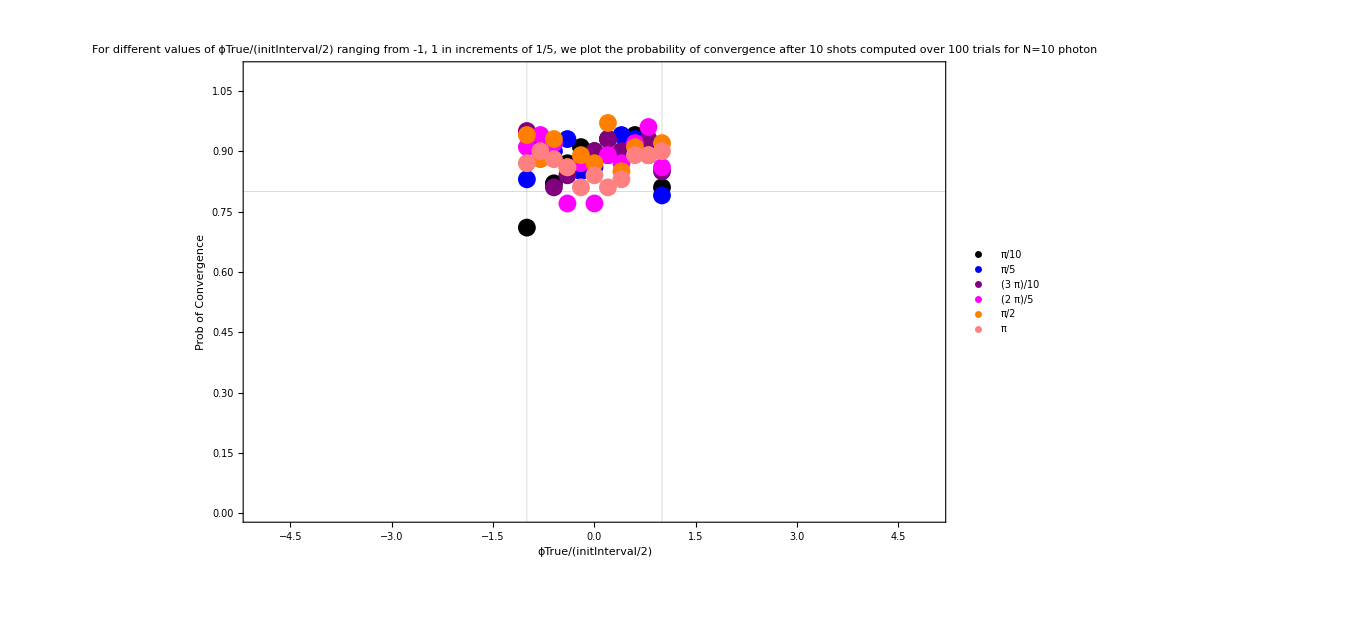

```mathematica
plot101=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=10 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

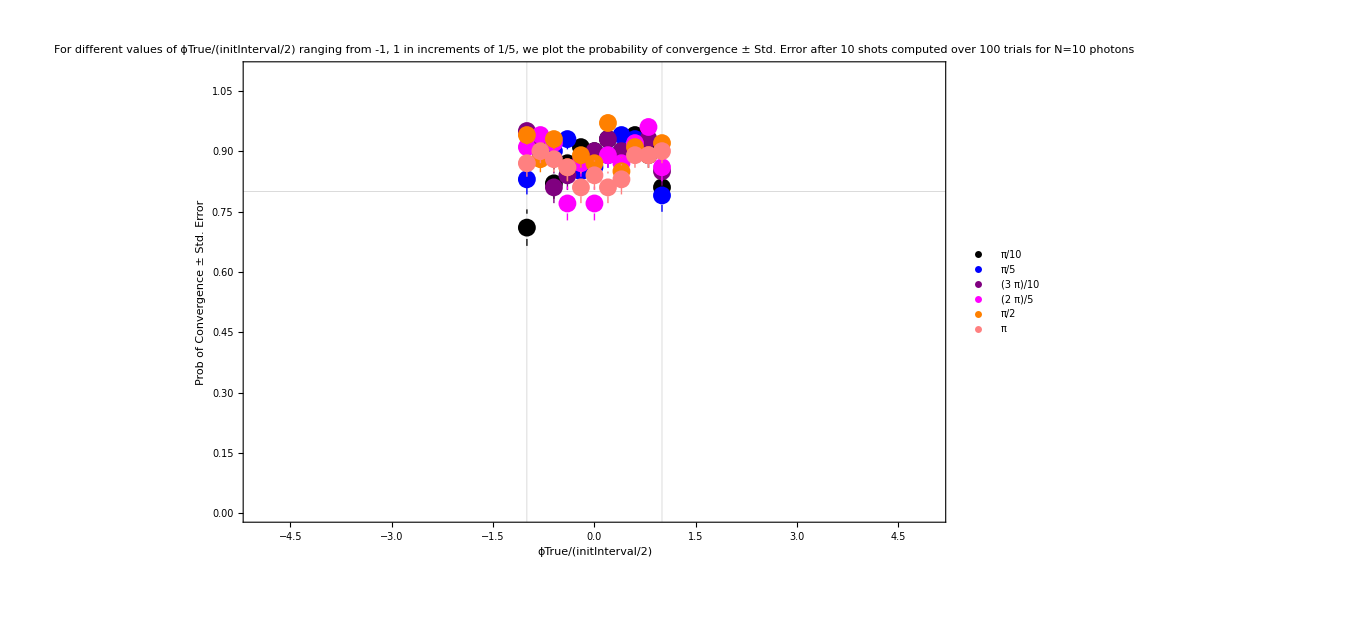

```mathematica
plot102=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=10 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

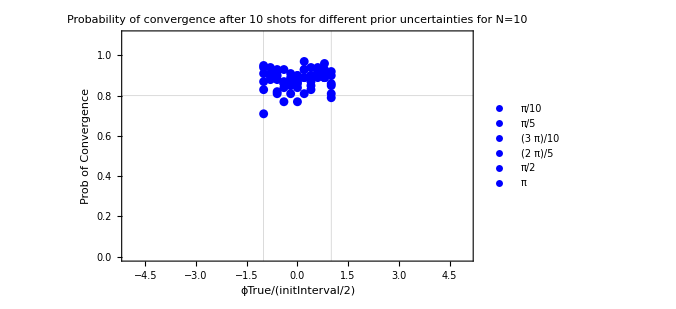

```mathematica
plot103=Show[ListPlot[plot[[1,1]],PlotStyle->{Blue, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=10",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Blue, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Blue,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Blue,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

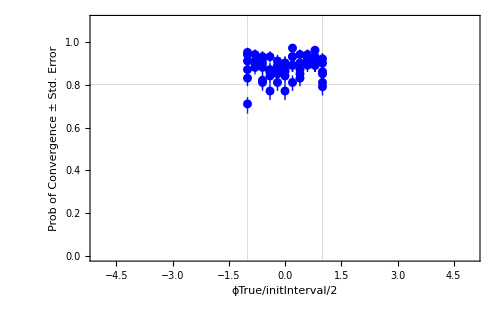

```mathematica
plot104=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Blue, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Blue, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Blue,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/initInterval/2",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

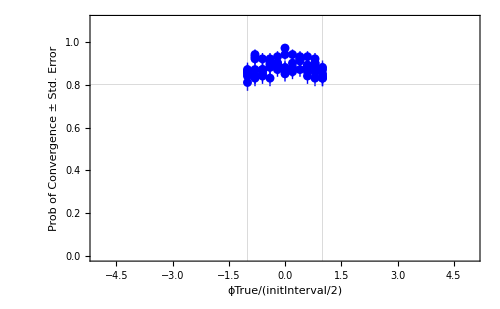
```mathematica
plot104=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average10
```

{0.8730.010,0.8830.010,0.8920.009,0.8800.010,0.9010.009,0.8620.010}

```mathematica
Average10=Around[Mean[Table[Average10[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average10[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8820.010

```mathematica
Average10=0.8820.010
```

0.8820.010

```mathematica
Average10=Around[Average10[[1]],Sqrt[Average10[[1]](1-Average10[[1]])/100]]
```

0.8820.032

### Compare N=3,5,7,10

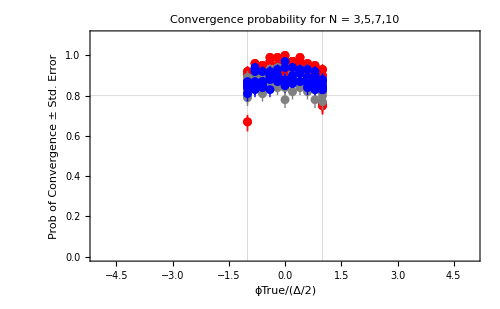

```mathematica
Show[plot34,plot54,plot74,plot104,FrameLabel->{{Style["Prob of Convergence ± Std. Error",Thickness[Large]],None},{HoldForm["\!\(\*FractionBox[\(ϕTrue\), \(Δ/2\)]\)"],None}},PlotLabel->"Convergence probability for N = 3,5,7,10", LabelStyle->{GrayLevel[0]}]
```

```mathematica
plot104=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Blue, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Blue, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"N=10"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Blue,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/initInterval/2",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
AverageConvergence={Average3,Average5,Average7,Average10}
```

{0.9120.028,0.8950.031,0.8960.031,0.8820.032}

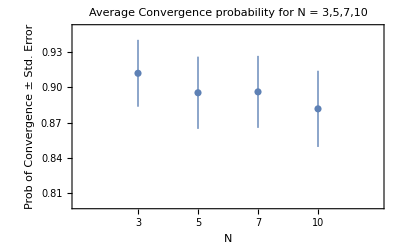

```mathematica
ListPlot[AverageConvergence,PlotRange->{{-0,5},{0.8,0.95}},PlotLabel->"Average Convergence probability for N = 3,5,7,10", Frame->True,FrameLabel-> {"N","Prob of Convergence ± Std. Error"},FrameTicks->{{Automatic,Automatic},{{{1,"3"},{2,"5"},{3,"7"},{4,"10"}},Automatic}}]
```

```mathematica
AverageConvergence2=MatrixForm[{{Average3[[1]], Average3[[2]]},{Average5[[1]], Average5[[2]]},{Average7[[1]], Average7[[2]]},{Average10[[1]], Average10[[2]]}}]
```

(0.900303 | 0.0286173
0.877727 | 0.0320042
0.867879 | 0.0333102
0.881515 | 0.03184)

```mathematica
Mean[AverageConvergence2[[1]]]
```

{0.881856,0.0314429}

#### Compare average convergence probability of adaptive with semi-adaptive

```mathematica
(*Semi-Adaptive*)
```

```mathematica
AverageConvergenceSA={0.9000.029,0.8780.032,0.8680.033,0.8820.032}
```

{0.9000.029,0.8780.032,0.8680.033,0.8820.032}

```mathematica
(*Adaptive*)
```

```mathematica
AverageConvergenceA={0.9120.028,0.8950.031,0.8960.031,0.8820.032}
```

{0.9120.028,0.8950.031,0.8960.031,0.8820.032}

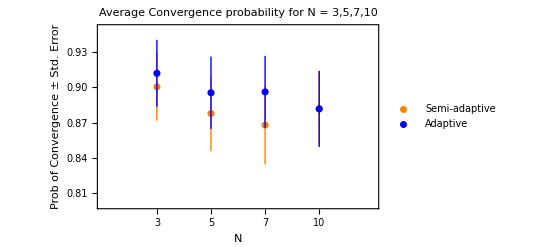

```mathematica
Show[ListPlot[AverageConvergenceSA, PlotStyle->Orange, PlotLegends->{"Semi-adaptive"}],ListPlot[AverageConvergenceA ,PlotStyle->Blue,PlotLegends->{"Adaptive"}],PlotRange->{{-0,5},{0.8,0.95}},PlotLabel->"Average Convergence probability for N = 3,5,7,10", Frame->True,FrameLabel-> {"N","Prob of Convergence ± Std. Error"},AxesOrigin->{0,0},FrameTicks->{{Automatic,Automatic},{{{1,"3"},{2,"5"},{3,"7"},{4,"10"}},Automatic}}]
```